# Parameters & Configuration

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
Omm=0.3111;
Oml=1-Omm;
H0=1/2997.9;
Lp4=4;
```

```mathematica
h=0.6766
```

0.6766

## Data imput

## Covariance Integrals

```mathematica
zsigma=Import["sigma8_CAMB.dat","Table"];
```

```mathematica
varcosmicMONObare=Import["integrals/varcosmic_mono_bare.dat","Table"];
varcosmicDIPbare=Import["integrals/varcosmic_dip_bare.dat","Table"];
varcosmicQUADbare=Import["integrals/varcosmic_quad_bare.dat","Table"];
varcosmicOCTbare=Import["integrals/varcosmic_oct_bare.dat","Table"];
varcosmicHEXAbare=Import["integrals/varcosmic_hexa_bare.dat","Table"];
varcosmic02bare=Import["integrals/varcosmic_mult02_bare.dat","Table"];
varcosmic04bare=Import["integrals/varcosmic_mult04_bare.dat","Table"];
varcosmic13bare=Import["integrals/varcosmic_mult13_bare.dat","Table"];
varcosmic24bare=Import["integrals/varcosmic_mult24_bare.dat","Table"];
varmixMONObare=Import["integrals/varmix_mono_bare.dat","Table"];
varmixDIPbare=Import["integrals/varmix_dip_bare.dat","Table"];
varmixQUADbare=Import["integrals/varmix_quad_bare.dat","Table"];
varmixOCTbare=Import["integrals/varmix_oct_bare.dat","Table"];
varmixHEXAbare=Import["integrals/varmix_hexa_bare.dat","Table"];
varmix02bare=Import["integrals/varmix_mult02_bare.dat","Table"];
varmix04bare=Import["integrals/varmix_mult04_bare.dat","Table"];
varmix13bare=Import["integrals/varmix_mult13_bare.dat","Table"];
varmix24bare=Import["integrals/varmix_mult24_bare.dat","Table"];
```

## Signals Integrals

```mathematica
nu1baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/nu1_z0_fid.dat","Table"];
```

```mathematica
nu1=Interpolation[nu1baretab];
```

```mathematica
nu1z0[d_]:=d H0 nu1[d];
```

MONOPOLE

```mathematica
mu0baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu0_z0_fid.dat","Table"];
```

```mathematica
mu0=Interpolation[mu0baretab];
```

```mathematica
mu0z0[d_]:= mu0[d];
```

QUADRUPOLE

```mathematica
mu2baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu2_z0_fid.dat","Table"];
```

```mathematica
mu2=Interpolation[mu2baretab];
```

```mathematica
mu2z0[d_]:=mu2[d];
```

OCTUPOLE

```mathematica
nu1baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/nu3_z0_fid.dat","Table"];
```

```mathematica
nu3=Interpolation[nu1baretab];
```

```mathematica
nu3z0[d_]:=d H0 nu3[d];
```

HEXADECAPOLE

```mathematica
mu4baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu4_z0_fid.dat","Table"];
mu4=Interpolation[mu4baretab];
mu4z0[d_]:= mu4[d];
```

```mathematica
mu0Lp4zbaretab=Table[mu0z0[d],{d,4,172,4}];
nu1Lp4zbaretab=Table[nu1z0[d],{d,4,172,4}];
mu2Lp4zbaretab=Table[mu2z0[d],{d,4,172,4}];
nu3Lp4zbaretab=Table[nu3z0[d],{d,4,172,4}];
mu4Lp4zbaretab=Table[mu4z0[d],{d,4,172,4}];
```

## Cosmology

```mathematica
r[z_]:=Integrate[1/(Sqrt[Omm x^3+Oml]),{x,1,1+z}];
```

```mathematica
r[0.15]/H0
```

433.566

```mathematica
D1[z_]:=5Omm/2(Omm(1+z)^3+1-Omm)^(1/2)NIntegrate[1/(Omm/x+(1-Omm) x^2)^(3/2),{x,0,1/(1+z)}]
```

```mathematica
fz[z_]:=1/(Omm+Oml/(1+z)^3)(-3Omm/2+5Omm/2/(1+z)/D1[z]);
```

```mathematica
HH[z_]=Sqrt[Omm(1+z)+(1-Omm)/(1+z)^2];
```

```mathematica
dD1dz[z_]:=(5 Omm /2) (3 Omm (1+z)^2/(2 Sqrt[Omm (1+z)^3 + Oml]) Integrate[(1+x)/(Sqrt[Omm(1+x)^3+Oml])^3,{x,z,Infinity}] - (1+z)/(Omm(1+z)^3+Oml))
```

```mathematica
Table[{D1[0],fz[0]},{i,1}]
```

{{0.785555,0.523414}}

```mathematica
OmegaLz[z_]:=1/(Omm (1+z)^3+Oml)
```

```mathematica
OmegaMz[z_]:= Omm (1+z)^3/(Omm(1+z)^3+Oml)
```

```mathematica
zSKA=List[0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95]; 
(* zSKA= List[0.20,0.28,0.36,0.44,0.53,0.64,0.79, 1.03, 1.31, 1.58, 1.86]; *)
```

```mathematica
ktot=Length[zSKA]
```

19

```mathematica
VzSKA=ParallelTable[4/3 Pi ( r[zSKA[[i]]+0.05]^3-r[zSKA[[i]]-0.05]^3)/H0^3 30000/41253,{i,1,ktot}];
fzSKA=ParallelTable[fz[zSKA[[i]]],{i,1,ktot}];
evolzSKA=ParallelTable[(D1[zSKA[[i]]]/D1[0])^2,{i,1,ktot}];
dzSKA=ParallelTable[r[zSKA[[i]]],{i,1,ktot}];
HzSKA=ParallelTable[HH[zSKA[[i]]],{i,1,ktot}];
dD1dzSKA=ParallelTable[dD1dz[zSKA[[i]]],{i,1,ktot}];
D1zSKA=Table[D1[i],{i,zSKA}];
D10=D1[0];
dfdzSKA=(3 Oml (1+zSKA)^2)/(Omm (1+zSKA)^3+Oml)^2 (-3 Omm/2 + 5 Omm /2 /((1+zSKA) D1zSKA)) - (5 Omm /2 )((1+zSKA)^3/(Omm(1+zSKA)^3+Oml))((D1zSKA+(1+zSKA) dD1dzSKA)/((1+zSKA)D1zSKA)^2);
rH0zSKA = r[zSKA];
```

```mathematica
VzSKA
```

{4.90045×10^8,1.20103×10^9,2.09836×10^9,3.09231×10^9,4.11482×10^9,5.11741×10^9,6.06784×10^9,6.94656×10^9,7.74333×10^9,8.45454×10^9,9.08098×10^9,9.62628×10^9,1.00957×10^10,1.04954×10^10,1.08317×10^10,1.11109×10^10,1.13393×10^10,1.15223×10^10,1.16654×10^10}

```mathematica
D1zSKA
```

{0.725792,0.688431,0.653295,0.620452,0.589882,0.561505,0.535207,0.510852,0.488297,0.467398,0.448017,0.430022,0.413292,0.397715,0.383189,0.369621,0.356928,0.345034,0.333872}

```mathematica
OmegaMzSKA=OmegaMz[zSKA]
```

{0.407165,0.468653,0.526309,0.579253,0.627097,0.669814,0.707623,0.740885,0.770035,0.795522,0.817786,0.837237,0.854242,0.869129,0.882186,0.893661,0.903769,0.912694,0.920593}

```mathematica
OmegaLzSKA=OmegaLz[zSKA]
```

{0.860552,0.771297,0.687605,0.610751,0.541302,0.479294,0.424412,0.376128,0.333815,0.296818,0.264499,0.236266,0.211581,0.18997,0.171017,0.15436,0.139688,0.126733,0.115266}

```mathematica
dOmegaLzSKA=- 3 Omm (1+zSKA)^2/(Omm(1+zSKA)^3+Oml)^2
```

{-0.914054,-0.86753,-0.804206,-0.731958,-0.656998,-0.583706,-0.51484,-0.451894,-0.395461,-0.345549,-0.301819,-0.263747,-0.230734,-0.202174,-0.177493,-0.156165,-0.137723,-0.121756,-0.107912}

Import CAMB results

```mathematica
Length[zsigma]
```

100

Redshift is displayed in the wrong order in zsigma. σ8 is given i

```mathematica
sigma8ztab=zsigma[[All,2]];
```

```mathematica
redshifts=zsigma[[All,1]];
```

```mathematica
zsigma8tab=Table[{redshifts[[i]],sigma8ztab[[i]]},{i,1,Length[redshifts]}];
```

```mathematica
sigma8z=Interpolation[zsigma8tab];
```

```mathematica
Sigma8z0=sigma8z[0]
```

0.814468

```mathematica
sigma8z[0]*D1[0.5]/D1[0]
```

0.627151

```mathematica
sigma8z[0.5]
```

0.627168

```mathematica
Sigma8zSKA=sigma8z[zSKA];
```

# Magnification & Evolution Bias

### Population parameters

```mathematica
b1=0.554;
b2=0.783;
bmeanzSKA=b1 Exp[b2 zSKA];
```

```mathematica
bB[m_, dbz_]:=bmeanzSKA+(m-1)dbz/m ;
bF[m_, dbz_]:=bmeanzSKA-dbz/m;
bTzSKA:=bmeanzSKA ;
```

```mathematica
bTzSKA
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

### Splitting 30% - 70% (m=10/3)

```mathematica
m=10/3;
```

```mathematica
db=1.2;
dbz=Table[db,{i,Length[zSKA]}];
```

#### Bright

```mathematica
nBSKA = 3/10;
```

```mathematica
smodelBzSKA = List[0.63665525,0.42367658,0.50881959,0.60522562,0.67778459,0.73405886,0.78698648,0.85067709,0.92313678,1.00034598,1.07877756,1.15621473,1.23564294,1.31904933,1.40610202,1.49646092,1.58855833,1.68141612,1.77443344];
```

```mathematica
fevolBzSKA = List[-2.35710791,0.50267603,0.00895782,-0.59492009,-0.49505863,-0.16404253,0.19264397,0.36952203,0.43853907,0.45440814,0.4833308,0.54007682,0.59932034,0.6323595,0.65280044,0.66681915,0.69110994,0.7429895,0.81482988];
```

```mathematica
bBzSKA = bB[m,dbz]
```

{1.46304,1.51379,1.56867,1.62801,1.69219,1.7616,1.83666,1.91784,2.00563,2.10056,2.20323,2.31426,2.43434,2.56419,2.70462,2.85649,3.02073,3.19834,3.39042}

#### Faint

```mathematica
nFSKA = 7/10;
```

```mathematica
smodelzSKA = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
If[!ValueQ[m]||m!=3,m=1/(1-nFSKA);]
m
```

10/3

```mathematica
smodelFzSKA = (m/(m-1)) smodelzSKA -(1/(m-1)) smodelBzSKA
```

{-0.128184,0.0583469,0.133246,0.226934,0.34323,0.467545,0.587359,0.69865,0.803523,0.904826,1.00684,1.11062,1.21737,1.32493,1.43485,1.54726,1.6627,1.78189,1.90084}

```mathematica
fevolFzSKA = List[4.22894971,3.22955823,2.61765473,1.95918753,0.94948372,0.01885715,-0.72267224,-1.22839524,-1.57209693,-1.82896117,-2.03473879,-2.22488036,-2.39749383,-2.54686948,-2.68379003,-2.81081826,-2.93482756,-3.05441667,-3.14524578];
```

```mathematica
bFzSKA = bF[m,dbz]
```

{0.263042,0.313787,0.368665,0.428013,0.492194,0.561603,0.636665,0.71784,0.805627,0.900564,1.00323,1.11426,1.23434,1.36419,1.50462,1.65649,1.82073,1.99834,2.19042}

# Covariance

## Parameters

```mathematica
Redshift = List[0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95];
```

```mathematica
NbarzSKAlist=List[6.2 10^-2/h^3,3.63 10^-2/h^3,2.16 10^-2/h^3,1.31 10^-2/h^3,8.07 10^-3/h^3,5.11 10^-3/h^3,3.27 10^-3/h^3,2.11 10^-3/h^3,1.36 10^-3/h^3,8.7 10^-4/h^3,5.56 10^-4/h^3,3.53 10^-4/h^3,2.22 10^-4/h^3,1.39 10^-4/h^3,8.55 10^-5/h^3,5.2 10^-5/h^3,3.12 10^-5/h^3,1.83 10^-5/h^3,1.05 10^-5/h^3];
Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]
```

{{0.15,0.200168},{0.25,0.117195},{0.35,0.0697361},{0.45,0.0422937},{0.55,0.0260542},{0.65,0.0164978},{0.75,0.0105573},{0.85,0.00681219},{0.95,0.00439079},{1.05,0.00280882},{1.15,0.00179506},{1.25,0.00113967},{1.35,0.000716732},{1.45,0.000448765},{1.55,0.000276039},{1.65,0.000167883},{1.75,0.00010073},{1.85,0.000059082},{1.95,0.0000338995}}

```mathematica
NbarzSKAfint= Interpolation[Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]];
NbarzSKA = NbarzSKAfint[zSKA]
```

{0.200168,0.117195,0.0697361,0.0422937,0.0260542,0.0164978,0.0105573,0.00681219,0.00439079,0.00280882,0.00179506,0.00113967,0.000716732,0.000448765,0.000276039,0.000167883,0.00010073,0.000059082,0.0000338995}

```mathematica
NtotSKA=Sum[NbarzSKA[[k]]VzSKA[[k]],{k,1,Length[zSKA]}]
```

9.23016×10^8

```mathematica
(*nBSKA=1/m;*)
(*nFSKA=1-nBSKA;*)
nBzSKA=Table[nBSKA, {i,Length[zSKA]}];
nFzSKA=Table[nFSKA, {i,Length[zSKA]}];
```

```mathematica
nBzSKA
```

{3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10}

```mathematica
nFzSKA
```

{7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10}

```mathematica
NbarBzSKA=NbarzSKA*nBzSKA
```

{0.0600505,0.0351586,0.0209208,0.0126881,0.00781626,0.00494933,0.00316718,0.00204366,0.00131724,0.000842645,0.000538518,0.000341901,0.00021502,0.000134629,0.0000828116,0.000050365,0.000030219,0.0000177246,0.0000101699}

```mathematica
NbarFzSKA=NbarzSKA*nFzSKA
```

{0.140118,0.0820368,0.0488153,0.0296056,0.0182379,0.0115484,0.00739009,0.00476853,0.00307355,0.00196617,0.00125654,0.000797768,0.000501713,0.000314135,0.000193227,0.000117518,0.000070511,0.0000413574,0.0000237297}

Coefficient for the mixed terms

```mathematica
coeff2popSKA=(evolzSKA/(VzSKA*NbarzSKA))
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffFSKA=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA /nBzSKA
```

{2.9008×10^-8,1.81879×10^-8,1.57546×10^-8,1.58995×10^-8,1.75318×10^-8,2.01724×10^-8,2.41537×10^-8,2.97893×10^-8,3.78812×10^-8,4.9692×10^-8,6.65124×10^-8,9.10478×10^-8,1.2751×10^-7,1.81406×10^-7,2.65268×10^-7,3.95622×10^-7,6.0248×10^-7,9.44614×10^-7,1.52263×10^-6}

```mathematica
coeffFSKA/nFzSKA
```

{1.2432×10^-8,7.79481×10^-9,6.75196×10^-9,6.81408×10^-9,7.51364×10^-9,8.64533×10^-9,1.03516×10^-8,1.27668×10^-8,1.62348×10^-8,2.12966×10^-8,2.85053×10^-8,3.90205×10^-8,5.46473×10^-8,7.77456×10^-8,1.13686×10^-7,1.69552×10^-7,2.58206×10^-7,4.04834×10^-7,6.52554×10^-7}

Coefficients for the Cosmic Variance

```mathematica
coeffCCSKA=evolzSKA^2/VzSKA
```

{1.48698×10^-9,4.91113×10^-10,2.27956×10^-10,1.25847×10^-10,7.72686×10^-11,5.10105×10^-11,3.55097×10^-11,2.57457×10^-11,1.92798×10^-11,1.48236×10^-11,1.16503×10^-11,9.3282×10^-12,7.589×10^-12,6.26012×10^-12,5.22696×10^-12,4.41133×10^-12,3.75864×10^-12,3.23×10^-12,2.79714×10^-12}

Coefficients needed for the cosmic variance of the dipole from relativistic effects

```mathematica
cBzSKA=(5smodelBzSKA +(2-5smodelBzSKA)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2-fevolBzSKA)fzSKA
```

{-1.70391,0.895284,0.592824,0.630427,0.480152,0.279389,0.0786685,0.00333885,0.0248213,0.116481,0.226818,0.340321,0.472092,0.646354,0.851276,1.08106,1.31899,1.54657,1.7686}

```mathematica
cFzSKA=(5smodelFzSKA +(2-5smodelFzSKA)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2- fevolFzSKA)fzSKA
```

{9.13213,3.51792,2.0517,1.29866,1.16499,1.29248,1.54051,1.79292,2.04051,2.30254,2.58099,2.8947,3.23377,3.58883,3.964,4.35837,4.77599,5.21419,5.6457}

```mathematica
indist=5;
Acc =1.0 ;
```

```mathematica
distances=Table[d,{d,4,172,4}]
```

{4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
Table[distances[[d]],{d,indist,Length[distances]}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
maxsep=Length[distances]-3
```

40

```mathematica
dists =Table[distances[[d]],{d,indist,maxsep}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160}

```mathematica
dtot =Length[dists]
```

36

```mathematica
ldist=maxsep-(indist-1)
```

36

```mathematica
8 ldist
```

288

```mathematica
ktot=Length[zSKA]
```

19

```mathematica
dmin =distances[[indist]];
dmax =  distances[[maxsep]];
```

```mathematica
{dmin, dmax}
```

{20,160}

## Multipole’s Coefficients

### Cosmic Variance

#### Definitions

```mathematica
G[n_,m_,a_,b_]:=Integrate[LegendreP[n,x]LegendreP[m,x]LegendreP[a,x]LegendreP[b,x],{x,-1,1}]
```

```mathematica
alpha0[bL_,bM_,f_]:=bL bM +(bL+bM)/3 f+f^2/5
alpha2[bL_,bM_,f_]:=2/3(bL+bM) f+4f^2/7
alpha4[bL_,bM_,f_]:=8f^2/35
```

```mathematica
coeffvarianceCC[n_,m_,bL_,bM_,bN_,bP_,f_]:=
Collect[
1/4((alpha0[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha0[bM, bN,f])G[n,m,0,0]+(alpha0[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha2[bM, bN,f])G[n,m,0,2]+(alpha0[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha4[bM, bN,f])G[n,m,0,4]+(alpha2[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha0[bM, bN,f])G[n,m,2,0]+(alpha2[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha2[bM, bN,f])G[n,m,2,2]+(alpha2[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha4[bM, bN,f])G[n,m,2,4]+(alpha4[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha0[bM, bN,f])G[n,m,4,0]+(alpha4[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha2[bM, bN,f])G[n,m,4,2]+(alpha4[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha4[bM, bN,f])G[n,m,4,4]),f,Simplify]
```

```mathematica
corrCC[n_,m_]:=If[n==m,1,(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCC[n_,m_,bL_,bM_,bN_,bP_,f_]:= corrCC[n,m]coeffvarianceCC[n,m,bL,bM,bN,bP,f]
```

COSMIC VARIANCE (DIPOLE)

```mathematica
alpha1[bL_,bM_,cL_,cM_,f_]:=cL(bM+3f/5)-cM(bL+3f/5)
alpha3[bL_,bM_,cL_,cM_,f_]:=2f/5(cL-cM)
```

```mathematica
coeffcovCCrel[n_,m_,bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=corrCC[n,m]Collect[(alpha1[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[n,m,1,1]+alpha1[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[n,m,1,3]+alpha3[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[n,m,3,1]+alpha3[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[n,m,3,3]),f,Simplify]
```

```mathematica
coeffvarCCrelSKAz[n_,m_,bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=evolzSKA^2 /VzSKA /4HzSKA^2coeffcovCCrel[n,m,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

```mathematica
varcosmicMONOzbaretab=Table[varcosmicMONObare,{i,Length[zSKA]}];
```

```mathematica
coeffvarianceCC[1,1,bL,bM,bL,bM,f]
```

0

```mathematica
coeffcovCCrel[1,1,bL,bM,bL,bM,cL,cM,cL,cM,f]
```

2/5 (bM cL-bL cM)^2+4/7 (cL-cM) (bM cL-bL cM) f+2/9 (cL-cM)^2 f^2

```mathematica
coeffcovCCrel[3,3,bL,bM,bL,bM,cL,cM,cL,cM,f]
```

46/315 (bM cL-bL cM)^2+52/231 (cL-cM) (bM cL-bL cM) f+14/143 (cL-cM)^2 f^2

```mathematica
coeffcovCCrel[1,3,bL,bM,bL,bM,cL,cM,cL,cM,f]
```

-21 (4/35 (bM cL-bL cM)^2+16/63 (cL-cM) (bM cL-bL cM) f+4/33 (cL-cM)^2 f^2)

```mathematica
corrCC[3,3]
```

1

```mathematica
corrCC[1,3]
```

-21

```mathematica
corrCC[1,3]coeffcovCCrel[1,3,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

441 (4/35 (bM cL-bL cM) (bP cN-bN cP)-8/63 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+4/33 (cL-cM) (cN-cP) f^2)

From 4 to 172 Mpc/h

```mathematica
varcosmicMONObare[[5,1]]
```

4.

```mathematica
varcosmicMONObare[[4,2]]
```

4.

```mathematica
varcosmicMONObare[[47,1]]
```

172.

```mathematica
varcosmicMONObare[[4,44]]
```

172.

```mathematica
4 i /. i-> 1
```

4

```mathematica
4 i /. i -> 43
```

172

```mathematica
varcosmicQUADzbaretab=Table[varcosmicQUADbare,{i,Length[zSKA]}];
```

```mathematica
varcosmicHEXAzbaretab=Table[varcosmicHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varcosmic02zbaretab=Table[varcosmic02bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic04zbaretab=Table[varcosmic04bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic24zbaretab=Table[varcosmic24bare,{i,Length[zSKA]}];
varcosmicDIPzbaretab=Table[varcosmicDIPbare, {i,Length[zSKA]}];
varcosmicOCTzbaretab=Table[varcosmicOCTbare, {i,Length[zSKA]}];
varcosmic13zbaretab=Table[varcosmic13bare, {i,Length[zSKA]}];
```

#### Monopole

```mathematica
coeffvarCC00=coeffvarCC[0,0,bL,bM,bN,bP,f]
```

bL bM bN bP+1/3 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+1/5 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+1/7 (bL+bM+bN+bP) f^3+f^4/9

Monopole - 1 Population

```mathematica
coeffvarCC[0,0,B,B,B,B,f]
```

B^4+(4 B^3 f)/3+(6 B^2 f^2)/5+(4 B f^3)/7+f^4/9

```mathematica
coeffvarCC1pop00BzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{1.23118×10^-8,4.79205×10^-9,2.61351×10^-9,1.69183×10^-9,1.21678×10^-9,9.40986×10^-10,7.68124×10^-10,6.54308×10^-10,5.77219×10^-10,5.24565×10^-10,4.89188×10^-10,4.66757×10^-10,4.54613×10^-10,4.51151×10^-10,4.55473×10^-10,4.67195×10^-10,4.86342×10^-10,5.13294×10^-10,5.4877×10^-10}

```mathematica
coeffvarCC1pop00FzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{1.47981×10^-10,7.86595×10^-11,5.6063×10^-11,4.58735×10^-11,4.06591×10^-11,3.80028×10^-11,3.69311×10^-11,3.70079×10^-11,3.80389×10^-11,3.99579×10^-11,4.27793×10^-11,4.6579×10^-11,5.14875×10^-11,5.76913×10^-11,6.54405×10^-11,7.50594×10^-11,8.69637×10^-11,1.01682×10^-10,1.19885×10^-10}

```mathematica
varCCMONOBrightLp4d4to172zSKA=Table[coeffvarCC1pop00BzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONOFaintLp4d4to172zSKA=Table[coeffvarCC1pop00FzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47},{j,2,44}];
```

```mathematica
coeffvarCC1pop00BFzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{1.22256×10^-9,5.64218×10^-10,3.56184×10^-10,2.62039×10^-10,2.11184×10^-10,1.81015×10^-10,1.62367×10^-10,1.50932×10^-10,1.44482×10^-10,1.41802×10^-10,1.42229×10^-10,1.45434×10^-10,1.51306×10^-10,1.59904×10^-10,1.71429×10^-10,1.86218×10^-10,2.04751×10^-10,2.2767×10^-10,2.55806×10^-10}

```mathematica
varCCMONOBrightFaintLp4d4to172zSKA=Table[coeffvarCC1pop00BFzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations

```mathematica
coeffvarCC[0,0,B,F,B,F,f]
```

f^4/9+B^2 F^2+2/7 f^3 (B+F)+2/3 B f F (B+F)+1/5 f^2 (B^2+4 B F+F^2)

```mathematica
coeffvarCC2pop00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.22256×10^-9,5.64218×10^-10,3.56184×10^-10,2.62039×10^-10,2.11184×10^-10,1.81015×10^-10,1.62367×10^-10,1.50932×10^-10,1.44482×10^-10,1.41802×10^-10,1.42229×10^-10,1.45434×10^-10,1.51306×10^-10,1.59904×10^-10,1.71429×10^-10,1.86218×10^-10,2.04751×10^-10,2.2767×10^-10,2.55806×10^-10}

```mathematica
varCCMONO2popLp4d4to172zSKA=Table[coeffvarCC2pop00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole 1 pop - Monopole 2 pop

```mathematica
coeffvarCCBright2pop00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{3.76041×10^-9,1.60217×10^-9,9.44213×10^-10,6.53985×10^-10,4.99432×10^-10,4.07671×10^-10,3.49599×10^-10,3.1166×10^-10,2.86839×10^-10,2.71241×10^-10,2.62607×10^-10,2.59615×10^-10,2.61524×10^-10,2.67982×10^-10,2.78929×10^-10,2.9454×10^-10,3.15211×10^-10,3.41554×10^-10,3.74418×10^-10}

```mathematica
coeffvarCCFaint2pop00zSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{4.17525×10^-10,2.07242×10^-10,1.39284×10^-10,1.0826×10^-10,9.16484×10^-11,8.21545×10^-11,7.68075×10^-11,7.42216×10^-11,7.37035×10^-11,7.49081×10^-11,7.76898×10^-11,8.20342×10^-11,8.80264×10^-11,9.58394×10^-11,1.05733×10^-10,1.18063×10^-10,1.33293×10^-10,1.52021×10^-10,1.75004×10^-10}

```mathematica
varCCMONOBrigth2popLp4d4to172zSKA=Table[coeffvarCCBright2pop00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCCMONOFaint2popLp4d4to172zSKA= Table[coeffvarCCFaint2pop00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole

```mathematica
coeffvarCC[1,1,B,F,B,F,f]
```

0

```mathematica
coeffcovCCrel[1,1,B,F,B,F,cB,cF,cB,cF,f]
```

2/9 (cB-cF)^2 f^2+2/5 (B cF-cB F)^2+4/7 (cB-cF) f (-B cF+cB F)

```mathematica
coeffvarCC11relzSKA=coeffvarCCrelSKAz[1,1,bBzSKA,bFzSKA,bBzSKA,bFzSKA,cBzSKA,cFzSKA,cBzSKA,cFzSKA,fzSKA]
```

{4.50772×10^-8,1.61169×10^-9,2.542×10^-10,4.74561×10^-11,2.66207×10^-11,2.86321×10^-11,3.64433×10^-11,4.10839×10^-11,4.32047×10^-11,4.45577×10^-11,4.64218×10^-11,4.97985×10^-11,5.39644×10^-11,5.80589×10^-11,6.25203×10^-11,6.74806×10^-11,7.35623×10^-11,8.12898×10^-11,8.96629×10^-11}

```mathematica
varCCDIPrelLp4d4to172zSKA=Table[coeffvarCC11relzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffcovCCrel[1,1,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

2/5 (bM cL-bL cM) (bP cN-bN cP)-2/7 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+2/9 (cL-cM) (cN-cP) f^2

```mathematica
Simplify[Collect[coeffcovCCrel[1,1,bN,bP,bL,bM,cN,cP,cL,cM,f]-coeffcovCCrel[1,1,bL,bM,bN,bP,cL,cM,cN,cP,f],f]]
```

0

#### Quadrupole

```mathematica
coeffvarCC[2,2,B,B,B,B,f]
```

B^4/5+(44 B^3 f)/105+(18 B^2 f^2)/35+(68 B f^3)/231+(83 f^4)/1287

Cuadrupole - 1 Population

```mathematica
coeffvarCC1pop22BzSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{3.31499×10^-9,1.30537×10^-9,7.17464×10^-10,4.66466×10^-10,3.35967×10^-10,2.59545×10^-10,2.11206×10^-10,1.79042×10^-10,1.5696×10^-10,1.41585×10^-10,1.30935×10^-10,1.23795×10^-10,1.19409×10^-10,1.17303×10^-10,1.17195×10^-10,1.18938×10^-10,1.22489×10^-10,1.27894×10^-10,1.35279×10^-10}

```mathematica
coeffvarCC1pop22FzSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{6.70958×10^-11,3.4836×10^-11,2.42193×10^-11,1.93035×10^-11,1.66426×10^-11,1.51122×10^-11,1.42529×10^-11,1.38504×10^-11,1.37985×10^-11,1.40458×10^-11,1.45729×10^-11,1.53821×10^-11,1.64927×10^-11,1.79394×10^-11,1.9773×10^-11,2.2062×10^-11,2.48954×10^-11,2.83876×10^-11,3.26839×10^-11}

```mathematica
varCCQUADBrightLp4d4to172zSKA= Table[coeffvarCC1pop22BzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUADFaintLp4d4to172zSKA= Table[coeffvarCC1pop22FzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC1pop22BFzSKA = coeffCCSKA coeffvarCC[2,2,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{4.45571×10^-10,2.02988×10^-10,1.26278×10^-10,9.14008×10^-11,7.23693×10^-11,6.0869×10^-11,5.35251×10^-11,4.87431×10^-11,4.5689×10^-11,4.38974×10^-11,4.31005×10^-11,4.31465×10^-11,4.39584×10^-11,4.55119×10^-11,4.78244×10^-11,5.09503×10^-11,5.49796×10^-11,6.00403×10^-11,6.63035×10^-11}

```mathematica
varCCQUADBrightFaintLp4d4to172zSKA = Table[coeffvarCC1pop22BFzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Cuadrupole - 2 populations

```mathematica
coeffvarCC2pop22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{4.45571×10^-10,2.02988×10^-10,1.26278×10^-10,9.14008×10^-11,7.23693×10^-11,6.0869×10^-11,5.35251×10^-11,4.87431×10^-11,4.5689×10^-11,4.38974×10^-11,4.31005×10^-11,4.31465×10^-11,4.39584×10^-11,4.55119×10^-11,4.78244×10^-11,5.09503×10^-11,5.49796×10^-11,6.00403×10^-11,6.63035×10^-11}

```mathematica
varCCQUAD2popLp4d4to172zSKA=Table[coeffvarCC2pop22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCBright2pop22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.18813×10^-9,5.05119×10^-10,2.96263×10^-10,2.03745×10^-10,1.54182×10^-10,1.24503×10^-10,1.05476×10^-10,9.27916×10^-11,8.42069×10^-11,7.84657×10^-11,7.4828×10^-11,7.28473×10^-11,7.22565×10^-11,7.29061×10^-11,7.47313×10^-11,7.77325×10^-11,8.19671×10^-11,8.75461×10^-11,9.46359×10^-11}

```mathematica
coeffvarCCFaint2pop22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.71581×10^-10,8.34952×10^-11,5.49406×10^-11,4.1751×10^-11,3.45129×10^-11,3.01766×10^-11,2.74946×10^-11,2.58766×10^-11,2.50172×10^-11,2.47512×10^-11,2.49917×10^-11,2.56996×10^-11,2.68697×10^-11,2.85233×10^-11,3.07056×10^-11,3.34856×10^-11,3.69586×10^-11,4.12498×10^-11,4.652×10^-11}

```mathematica
varCCQUADBright2popLp4d4to172zSKA=Table[coeffvarCCBright2pop00zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUADFaint2popLp4d4to172zSKA=Table[coeffvarCCFaint2pop00zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Octupole

```mathematica
coeffvarCC[3,3,b,b,b,b,f]
```

0

```mathematica
coeffcovCCrel[3,3,B,F,B,F,cB,cF,cB,cF,f]
```

14/143 (cB-cF)^2 f^2+46/315 (B cF-cB F)^2+52/231 (cB-cF) f (-B cF+cB F)

```mathematica
coeffCCSKA coeffvarCC[3,3,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.27363×10^-26,3.19479×10^-27,-2.07606×10^-27,-9.0053×10^-28,-4.77516×10^-27,5.88452×10^-27,-4.80476×10^-27,-1.33985×10^-28,1.23747×10^-27,-3.47792×10^-27,-2.27364×10^-28,4.41764×10^-27,-1.92865×10^-27,1.3846×10^-27,-1.8316×10^-27,-3.41681×10^-27,1.15408×10^-27,4.4545×10^-28,6.25942×10^-28}

```mathematica
coeffvarCC33relzSKA=coeffvarCCrelSKAz[3,3,bBzSKA,bFzSKA,bBzSKA,bFzSKA,cBzSKA,cFzSKA,cBzSKA,cFzSKA,fzSKA]
```

{1.71859×10^-8,6.08129×10^-10,9.59097×10^-11,1.77949×10^-11,1.0014×10^-11,1.08392×10^-11,1.38509×10^-11,1.56225×10^-11,1.64131×10^-11,1.68997×10^-11,1.75776×10^-11,1.88271×10^-11,2.03707×10^-11,2.18804×10^-11,2.35231×10^-11,2.5349×10^-11,2.75928×10^-11,3.04507×10^-11,3.35451×10^-11}

```mathematica
varCCOCTrelLp4d4to172zSKA=Table[coeffvarCC33relzSKA[[k]] varcosmicOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffcovCCrel[3,3,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

46/315 (bM cL-bL cM) (bP cN-bN cP)-26/231 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+14/143 (cL-cM) (cN-cP) f^2

```mathematica
Simplify[Collect[coeffcovCCrel[3,3,bN,bP,bL,bM,cN,cP,cL,cM,f]-coeffcovCCrel[3,3,bL,bM,bN,bP,cL,cM,cN,cP,f],f]]
```

0

```mathematica
Diagonal[varCCOCTrelLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{3.09987×10^-12,2.82882×10^-11,9.0298×10^-11,1.91672×10^-10,3.2837×10^-10,4.93791×10^-10,6.80799×10^-10,8.82724×10^-10,1.09377×10^-9,1.30917×10^-9,1.5256×10^-9,1.74126×10^-9,1.95305×10^-9,2.15649×10^-9,2.34324×10^-9}

```mathematica
Diagonal[varCCDIPrelLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{5.75932×10^-10,1.813×10^-9,3.23682×10^-9,4.62435×10^-9,5.87853×10^-9,6.96407×10^-9,7.8761×10^-9,8.62427×10^-9,9.22479×10^-9,9.69641×10^-9,1.00588×10^-8,1.0332×10^-8,1.05363×10^-8,1.06881×10^-8,1.07971×10^-8}

```mathematica
Diagonal[varCCQUADBrightLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{5.87456×10^-6,0.0000127488,0.0000174622,0.0000202821,0.0000217447,0.0000222864,0.0000222207,0.0000217645,0.0000210676,0.0000202411,0.0000193648,0.0000184765,0.0000175099,0.000016404,0.0000152436}

#### Hexadecapole

```mathematica
coeffvarCC44=coeffvarCC[4,4,bL,bM,bN,bP,f]
```

1/9 bL bM bN bP+13/231 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(643 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/15015+(109 (bL+bM+bN+bP) f^3)/3003+(79 f^4)/2431

Hexadecapole - TOTAL population

```mathematica
coeffvarCC2pop44=coeffvarCC[4,4,B,B,B,B,f]
```

B^4/9+(52 B^3 f)/231+(1286 B^2 f^2)/5005+(436 B f^3)/3003+(79 f^4)/2431

```mathematica
bTzSKA
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarCCtotpop44zSKA= coeffCCSKA coeffvarCC[4,4,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
varCCHEXAtotpopLp4d4to172zSKA=Table[coeffvarCCtotpop44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

Monopole/Cuadrupole - 1 Population

```mathematica
coeffvarCC[0,2,B,B,B,B,f]
```

-5 ((8 B^3 f)/15+(24 B^2 f^2)/35+(8 B f^3)/21+(8 f^4)/99)

```mathematica
coeffvarCC1pop02BzSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{-1.26224×10^-8,-5.10677×10^-9,-2.85562×10^-9,-1.87417×10^-9,-1.35398×10^-9,-1.04366×10^-9,-8.43592×10^-10,-7.07553×10^-10,-6.11593×10^-10,-5.42239×10^-10,-4.91432×10^-10,-4.54113×10^-10,-4.27×10^-10,-4.07905×10^-10,-3.95353×10^-10,-3.8835×10^-10,-3.86241×10^-10,-3.88625×10^-10,-3.95291×10^-10}

```mathematica
coeffvarCC1pop02FzSKA=coeffCCSKA coeffvarCC[0,2,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{-4.25336×10^-10,-2.1969×10^-10,-1.5171×10^-10,-1.19885×10^-10,-1.02262×10^-10,-9.16578×10^-11,-8.51075×10^-11,-8.11975×10^-11,-7.91863×10^-11,-7.86634×10^-11,-7.93998×10^-11,-8.12754×10^-11,-8.42429×10^-11,-8.83075×10^-11,-9.35175×10^-11,-9.99591×10^-11,-1.07756×10^-10,-1.17069×10^-10,-1.28101×10^-10}

```mathematica
varCCMONOQUADBrightLp4d4to172zSKA=Table[coeffvarCC1pop02BzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONOQUADFaintLp4d4to172zSKA=Table[coeffvarCC1pop02FzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC02BrightFaint=coeffCCSKA coeffvarCC[0,2,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{-2.61665×10^-9,-1.17789×10^-9,-7.22958×10^-10,-5.15369×10^-10,-4.01108×10^-10,-3.30932×10^-10,-2.84834×10^-10,-2.53317×10^-10,-2.3136×10^-10,-2.16092×10^-10,-2.05778×10^-10,-1.99332×10^-10,-1.96063×10^-10,-1.95535×10^-10,-1.97488×10^-10,-2.01787×10^-10,-2.084×10^-10,-2.17377×10^-10,-2.28842×10^-10}

```mathematica
varCCMONOQUADBrightFaintLp4d4to172zSKA=Table[coeffvarCC02BrightFaint[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole/Cuadrupole - 2 populations

```mathematica
coeffvarCC[0,2,B,F,B,F,f]
```

-5 ((8 f^4)/99+4/21 f^3 (B+F)+4/15 B f F (B+F)+4/35 f^2 (B^2+4 B F+F^2))

```mathematica
coeffvarCC2pop02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-2.61665×10^-9,-1.17789×10^-9,-7.22958×10^-10,-5.15369×10^-10,-4.01108×10^-10,-3.30932×10^-10,-2.84834×10^-10,-2.53317×10^-10,-2.3136×10^-10,-2.16092×10^-10,-2.05778×10^-10,-1.99332×10^-10,-1.96063×10^-10,-1.95535×10^-10,-1.97488×10^-10,-2.01787×10^-10,-2.084×10^-10,-2.17377×10^-10,-2.28842×10^-10}

```mathematica
varCCMONOQUAD2popLp4d4to172zSKA=Table[coeffvarCC2pop02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCBright2pop02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-6.12127×10^-9,-2.58471×10^-9,-1.50188×10^-9,-1.02066×10^-9,-7.61343×10^-10,-6.04531×10^-10,-5.02411×10^-10,-4.32587×10^-10,-3.83344×10^-10,-3.48042×10^-10,-3.22684×10^-10,-3.04756×10^-10,-2.92631×10^-10,-2.85238×10^-10,-2.81872×10^-10,-2.82087×10^-10,-2.85622×10^-10,-2.92363×10^-10,-3.02313×10^-10}

```mathematica
coeffvarCCFaint2pop02zSKA= coeffCCSKA coeffvarCC[0,2,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-1.06564×10^-9,-5.1374×10^-10,-3.34388×10^-10,-2.50909×10^-10,-2.0438×10^-10,-1.75697×10^-10,-1.57014×10^-10,-1.44576×10^-10,-1.36391×10^-10,-1.31321×10^-10,-1.28691×10^-10,-1.28089×10^-10,-1.29274×10^-10,-1.32118×10^-10,-1.36577×10^-10,-1.42671×10^-10,-1.50477×10^-10,-1.60125×10^-10,-1.71798×10^-10}

```mathematica
varCCMONOQUADBright2popLp4d4to172zSKA=Table[coeffvarCCBright2pop02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONOQUADFaint2popLp4d4to172zSKA=Table[coeffvarCCFaint2pop02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC[0,4,bL,bM,bN,bP,f]
```

9 (8/315 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+8/231 (bL+bM+bN+bP) f^3+(16 f^4)/429)

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC[0,4,B,B,T,T,f]
```

9 ((16 f^4)/429+16/231 f^3 (B+T)+8/315 f^2 (B^2+4 B T+T^2))

```mathematica
bTzSKA
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarCC1pop04BzSKA= coeffCCSKA coeffvarCC[0,4,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{1.28279×10^-9,5.5453×10^-10,3.26227×10^-10,2.22405×10^-10,1.65157×10^-10,1.29713×10^-10,1.06044×10^-10,8.93931×10^-11,7.72372×10^-11,6.81228×10^-11,6.11572×10^-11,5.57645×10^-11,5.15585×10^-11,4.8272×10^-11,4.57155×10^-11,4.37523×10^-11,4.22824×10^-11,4.1232×10^-11,4.05465×10^-11}

```mathematica
coeffvarCC1pop04FzSKA=coeffCCSKA coeffvarCC[0,4,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{3.94109×10^-10,1.8541×10^-10,1.17441×10^-10,8.54876×10^-11,6.7337×10^-11,5.58031×10^-11,4.79326×10^-11,4.23054×10^-11,3.81579×10^-11,3.50441×10^-11,3.26862×10^-11,3.09028×10^-11,2.95711×10^-11,2.86054×10^-11,2.79452×10^-11,2.75469×10^-11,2.73795×10^-11,2.74211×10^-11,2.76568×10^-11}

```mathematica
varCCMONOHEXABrightLp4d4to172zSKA=Table[coeffvarCC1pop04BzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONOHEXAFaintLp4d4to172zSKA=Table[coeffvarCC1pop04FzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC[0,4,B,F,T,T,f]
```

9 ((16 f^4)/429+8/231 f^3 (B+F+2 T)+8/315 f^2 (T (2 F+T)+B (F+2 T)))

```mathematica
coeffvarCC2pop04zSKA=  coeffCCSKA coeffvarCC[0,4,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{7.47745×10^-10,3.3492×10^-10,2.03324×10^-10,1.42581×10^-10,1.08629×10^-10,8.73493×10^-11,7.29883×10^-11,6.27986×10^-11,5.53141×10^-11,4.96842×10^-11,4.53831×10^-11,4.20696×10^-11,3.95135×10^-11,3.75549×10^-11,3.60802×10^-11,3.50075×10^-11,3.42771×10^-11,3.38455×10^-11,3.36811×10^-11}

```mathematica
varCCMONOHEXA2popLp4d4to172zSKA=Table[coeffvarCC2pop04zSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC[2,4,bL,bM,bN,bP,f]
```

-45 (4/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(136 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/3465+(116 (bL+bM+bN+bP) f^3)/3003+(16 f^4)/429)

Cuadrupole - 1 Population/Hexadecapole - TOTAL population

```mathematica
coeffvarCC[2,4,B,B,T,T,f]
```

-45 ((16 f^4)/429+(232 f^3 (B+T))/3003+8/105 B f T (B+T)+(136 f^2 (B^2+4 B T+T^2))/3465)

```mathematica
coeffvarCC1pop24BzSKA=coeffCCSKA coeffvarCC[2,4,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{-1.46892×10^-8,-6.26331×10^-9,-3.66835×10^-9,-2.5089×10^-9,-1.881×10^-9,-1.4996×10^-9,-1.25025×10^-9,-1.0792×10^-9,-9.58263×10^-10,-8.71409×10^-10,-8.08971×10^-10,-7.64854×10^-10,-7.35101×10^-10,-7.17109×10^-10,-7.0917×10^-10,-7.102×10^-10,-7.19579×10^-10,-7.3704×10^-10,-7.62616×10^-10}

```mathematica
coeffvarCC1pop24FzSKA=coeffCCSKA coeffvarCC[2,4,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{-2.91057×10^-9,-1.39402×10^-9,-9.02314×10^-10,-6.73599×10^-10,-5.46001×10^-10,-4.67137×10^-10,-4.15523×10^-10,-3.80889×10^-10,-3.57783×10^-10,-3.43089×10^-10,-3.34948×10^-10,-3.32227×10^-10,-3.34248×10^-10,-3.40643×10^-10,-3.51266×10^-10,-3.66147×10^-10,-3.85465×10^-10,-4.0954×10^-10,-4.38826×10^-10}

```mathematica
varCCQUADHEXABrightLp4d4to172zSKA=Table[coeffvarCC1pop24BzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUADHEXAFaintLp4d4to172zSKA=Table[coeffvarCC1pop24FzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Cuadrupole/Hexadecapole - 2 populations

```mathematica
coeffvarCC[2,4,B,F,T,T,f]
```

-45 ((16 f^4)/429+(116 f^3 (B+F+2 T))/3003+4/105 f T (F T+B (2 F+T))+(136 f^2 (T (2 F+T)+B (F+2 T)))/3465)

Cuadrupole - 2 Populations/Hexadecapole - TOTAL population

```mathematica
coeffvarCC2pop24zSKA= coeffCCSKA coeffvarCC[2,4,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{-6.70666×10^-9,-3.01989×10^-9,-1.85428×10^-9,-1.32208×10^-9,-1.02882×10^-9,-8.48418×10^-10,-7.29694×10^-10,-6.48346×10^-10,-5.91523×10^-10,-5.51872×10^-10,-5.24949×10^-10,-5.07966×10^-10,-4.99147×10^-10,-4.97368×10^-10,-5.01955×10^-10,-5.12561×10^-10,-5.29096×10^-10,-5.51684×10^-10,-5.80639×10^-10}

```mathematica
varCCQUADHEXA2popLp4d4to172zSKA=Table[coeffvarCC2pop24zSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole/Octupole

```mathematica
coeffvarCC[1,3,bL,bM,bN,bP,f]
```

0

Dipole/Octupole - 2 populations

```mathematica
coeffvarCC[1,3,B,F,B,F,f]
```

0

```mathematica
coeffcovCCrel[1,3,B,F,B,F,cB,cF,cB,cF,f]
```

-21 (4/33 (cB-cF)^2 f^2+4/35 (B cF-cB F)^2+16/63 (cB-cF) f (-B cF+cB F))

```mathematica
coeffCCSKA coeffvarCC[1,3,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-1.76051×10^-25,3.57817×10^-26,-5.81298×10^-26,5.50142×10^-26,1.82964×10^-26,-9.47718×10^-26,7.5675×10^-26,1.50063×10^-26,-4.00338×10^-26,4.21208×10^-26,3.09821×10^-26,-5.74294×10^-26,-7.18799×10^-27,-3.92248×10^-26,2.18976×10^-26,8.67786×10^-27,-1.34186×10^-26,4.84785×10^-26,7.33663×10^-27}

```mathematica
coeffvarCC2pop13zSKA=coeffvarCCrelSKAz [1,3,bBzSKA,bFzSKA,bBzSKA,bFzSKA,cBzSKA,cFzSKA,cBzSKA,cFzSKA,fzSKA]
```

{-3.44373×10^-7,-1.17291×10^-8,-1.84937×10^-9,-3.34622×10^-10,-1.90805×10^-10,-2.11718×10^-10,-2.74501×10^-10,-3.10171×10^-10,-3.24736×10^-10,-3.32393×10^-10,-3.43611×10^-10,-3.65892×10^-10,-3.93546×10^-10,-4.19993×10^-10,-4.48573×10^-10,-4.80259×10^-10,-5.19559×10^-10,-5.70145×10^-10,-6.24709×10^-10}

```mathematica
varCCDIPOCTrel2popLp4d4to172zSKA = Table[coeffvarCC2pop13zSKA[[k]] varcosmic13zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCCDIPOCTrel2popLp4d4to172zSKA[[1,1,1]]
```

-8.67989×10^-12

### Mixed terms

#### Definitions

```mathematica
coeffvarmixed[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=Collect[1/8(((alpha0[bM,bP,f]/NL KroneckerDelta[bL,bN]+(-1)^m alpha0[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha0[bL,bN,f]/NM KroneckerDelta[bM,bP]+(-1)^m alpha0[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,0,0]+((alpha2[bM,bP,f]/NL KroneckerDelta[bL,bN]+(-1)^m alpha2[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha2[bL,bN,f]/NM KroneckerDelta[bM,bP]+(-1)^m alpha2[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,2,0]+((alpha4[bM,bP,f]/NL KroneckerDelta[bL,bN]+(-1)^m alpha4[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha4[bL,bN,f]/NM KroneckerDelta[bM,bP]+(-1)^m alpha4[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,4,0]),f,Simplify]
```

```mathematica
coeffvarmixedJointHexa[n_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_,bN_,bP_,f_]:=
Collect[1/8(
2(alpha0[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha0[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nP G[n,m,0,0] 
+ 2(alpha2[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha2[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nPG[n,m,2,0] 
+ 2(alpha4[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha4[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nPG[n,m,4,0]
),f,Simplify]
```

```mathematica
coeffvarmixedHexa[l_,m_,nT_, oLT_,oMT_, bL_, bM_, bT_, f_]:=
Collect[1/8(
(1+(-1)^m)/nT (
(oMT alpha0[bL,bT,f] + (-1)^(l+m) oLT alpha0[bM,bT,f]) G[l,m,0,0]
+(oMT alpha2[bL,bT,f] + (-1)^(l+m) oLT alpha2[bM,bT,f]) G[l,m,2,0] 
+ (oMT alpha4[bL,bT,f] + (-1)^(l+m) oLT alpha4[bM,bT,f]) G[l,m,4,0])
),f,Simplify]
```

```mathematica
corrCP[n_,m_]:=If[n==m,1,2(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCPgeneral[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=corrCP[n,m]coeffvarmixed[n,m,NL,NM,bL,bM,bN,bP,f]
```

```mathematica
coeffvarCPJointHexa[n_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_,bN_,bP_,f_]:=corrCP[n,m]coeffvarmixedJointHexa[n,m,nN,nP,oLP,oMP,bL,bM,bN,bP,f]
```

```mathematica
coeffvarCPHexa[l_,m_,nT_, oLT_,oMT_, bL_, bM_, bT_, f_]:=corrCP[l,m]coeffvarmixedHexa[l,m,nT,oLT,oMT,bL,bM,bT,f]
```

```mathematica
varmixMONOzbaretab=Table[varmixMONObare,{i,Length[zSKA]}];
```

```mathematica
varmixDIPzbaretab=Table[varmixDIPbare,{i,Length[zSKA]}];
```

```mathematica
varmixQUADzbaretab=Table[varmixQUADbare, {i,Length[zSKA]}];
```

```mathematica
varmixOCTzbaretab=Table[varmixOCTbare, {i,Length[zSKA]}];
```

```mathematica
varmixHEXAzbaretab=Table[varmixHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varmix02zbaretab=Table[varmix02bare,{i,Length[zSKA]}];
```

```mathematica
varmix04zbaretab=Table[varmix04bare,{i,Length[zSKA]}];
```

```mathematica
varmix13zbaretab=Table[varmix13bare,{i,Length[zSKA]}];
```

```mathematica
varmix24zbaretab=Table[varmix24bare,{i,Length[zSKA]}];
```

#### Monopole

Monopole - 1 Population

```mathematica
coeffvarCPgeneral[0,0,N,N,B,B,B,B,f]
```

B^2/N+(2 B f)/(3 N)+f^2/(5 N)

```mathematica
coeffvarCP1pop00BzSKA=  coeffBSKA coeffvarCPgeneral[0,0,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{8.1467×10^-8,5.53434×10^-8,5.18952×10^-8,5.66686×10^-8,6.76121×10^-8,8.42156×10^-8,1.09254×10^-7,1.46176×10^-7,2.01969×10^-7,2.88398×10^-7,4.21059×10^-7,6.301×10^-7,9.66956×10^-7,1.51111×10^-6,2.43334×10^-6,4.00659×10^-6,6.75346×10^-6,0.0000117499,0.0000210703}

```mathematica
coeffvarCP1pop00FzSKA=coeffFSKA coeffvarCPgeneral[0,0,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{3.10902×10^-9,2.51737×10^-9,2.74964×10^-9,3.43646×10^-9,4.6288×10^-9,6.43894×10^-9,9.24816×10^-9,1.36014×10^-8,2.05334×10^-8,3.18697×10^-8,5.03438×10^-8,8.11766×10^-8,1.33719×10^-7,2.23515×10^-7,3.83689×10^-7,6.71324×10^-7,1.19877×10^-6,2.20302×10^-6,4.16098×10^-6}

```mathematica
varCPMONOBrightLp4d4to172zSKA=Table[coeffvarCP1pop00BzSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPMONOFaintLp4d4to172zSKA=Table[coeffvarCP1pop00FzSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCP1pop00BFzSKA=coeffBSKA coeffvarCPgeneral[0,0,nBzSKA,nFzSKA,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOBrightFaintLp4d4to172zSKA=Table[coeffvarCP1pop00BFzSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,0,nB,nF,B,F,B,F,f]
```

(f^2 (nB+nF) (1+B,F))/(20 nB nF)+(B^2 nB+F^2 nF+B F (nB+nF) B,F)/(4 nB nF)+(f (2 (B nB+F nF)+(B+F) (nB+nF) B,F))/(12 nB nF)

```mathematica
coeffvarCP2pop00zSKA= coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.05422×10^-8,7.39811×10^-9,7.16416×10^-9,8.07623×10^-9,9.94428×10^-9,1.27791×10^-8,1.71005×10^-8,2.35959×10^-8,3.36174×10^-8,4.94904×10^-8,7.44807×10^-8,1.14864×10^-7,1.81605×10^-7,2.92289×10^-7,4.84533×10^-7,8.20883×10^-7,1.42287×10^-6,2.54401×10^-6,4.68477×10^-6}

```mathematica
varCPMONO2popLp4d4to172zSKA=Table[coeffvarCP2pop00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPBright2pop00zSKA=coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.17374×10^-8,8.75667×10^-9,8.90611×10^-9,1.04479×10^-8,1.32917×10^-8,1.75479×10^-8,2.40129×10^-8,3.3754×10^-8,4.88329×10^-8,7.2801×10^-8,1.10687×10^-7,1.72101×10^-7,2.73838×10^-7,4.42856×10^-7,7.36656×10^-7,1.25083×10^-6,2.17075×10^-6,3.88251×10^-6,7.14666×10^-6}

```mathematica
varCPMONOBright2popLp4d4to172zSKA=Table[coeffvarCPBright2pop00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPFaint2pop00zSKA=coeff2popSKA coeffvarCPgeneral[0,0,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bBzSKA,fzSKA]
```

{5.03033×10^-9,3.75286×10^-9,3.81691×10^-9,4.47768×10^-9,5.69644×10^-9,7.52052×10^-9,1.02912×10^-8,1.4466×10^-8,2.09284×10^-8,3.12004×10^-8,4.74375×10^-8,7.37575×10^-8,1.17359×10^-7,1.89795×10^-7,3.1571×10^-7,5.3607×10^-7,9.30323×10^-7,1.66393×10^-6,3.06286×10^-6}

```mathematica
varCPMONOFaint2popLp4d4to172zSKA=Table[coeffvarCPFaint2pop00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole

Dipole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[1,1,nB,nF,B,F,B,F,f]
```

-(f^2 (nB+nF) (-1+B,F))/(28 nB nF)+(B^2 nB+F^2 nF-B F (nB+nF) B,F)/(12 nB nF)+(f (2 (B nB+F nF)-(B+F) (nB+nF) B,F))/(20 nB nF)

```mathematica
coeffvarCP2pop11zSKA= coeff2popSKA coeffvarCPgeneral[1,1,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{4.50524×10^-9,3.19305×10^-9,3.11156×10^-9,3.51877×10^-9,4.3348×10^-9,5.56086×10^-9,7.41462×10^-9,1.01787×10^-8,1.441×10^-8,2.10588×10^-8,3.14365×10^-8,4.80616×10^-8,7.52984×10^-8,1.20058×10^-7,1.97131×10^-7,3.30783×10^-7,5.67901×10^-7,1.00583×10^-6,1.83511×10^-6}

```mathematica
varCPDIP2popLp4d4to172zSKA=Table[coeffvarCP2pop11zSKA[[k]] varmixDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole

Quadrupole - 1 Population

```mathematica
coeffvarCPgeneral[2,2,n,n,B,B,B,B,f]
```

B^2/(5 n)+(22 B f)/(105 n)+(3 f^2)/(35 n)

```mathematica
coeffvarCP1pop22BzSKA=coeffBSKA coeffvarCPgeneral[2,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{1.87535×10^-8,1.28107×10^-8,1.2057×10^-8,1.31935×10^-8,1.57521×10^-8,1.96106×10^-8,2.5403×10^-8,3.39092×10^-8,4.67118×10^-8,6.64654×10^-8,9.66537×10^-8,1.44015×10^-7,2.19996×10^-7,3.42162×10^-7,5.48286×10^-7,8.98286×10^-7,1.50656×10^-6,2.60805×10^-6,4.6536×10^-6}

```mathematica
coeffvarCP1pop22FzSKA=coeffFSKA coeffvarCPgeneral[2,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{9.84135×10^-10,7.80725×10^-10,8.35443×10^-10,1.02283×10^-9,1.34963×10^-9,1.83936×10^-9,2.58899×10^-9,3.73297×10^-9,5.52787×10^-9,8.42124×10^-9,1.30663×10^-8,2.07102×10^-8,3.3562×10^-8,5.52364×10^-8,9.34396×10^-8,1.61244×10^-7,2.84215×10^-7,5.15991×10^-7,9.63543×10^-7}

```mathematica
varCPQUADBrightLp4d4to172zSKA=Table[coeffvarCP1pop22BzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUADFaintLp4d4to172zSKA=Table[coeffvarCP1pop22FzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCP1pop22BFzSKA=coeffFSKA coeffvarCPgeneral[2,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPQUADBrightFaintLp4d4to172zSKA=Table[coeffvarCP1pop22BFzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCP2pop22zSKA= coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.58338×10^-9,1.82799×10^-9,1.77917×10^-9,2.01024×10^-9,2.47501×10^-9,3.17409×10^-9,4.23199×10^-9,5.8107×10^-9,8.22943×10^-9,1.20337×10^-8,1.79778×10^-8,2.75112×10^-8,4.31489×10^-8,6.88815×10^-8,1.13251×10^-7,1.90304×10^-7,3.27209×10^-7,5.80429×10^-7,1.06067×10^-6}

```mathematica
varCPQUAD2popLp4d4to172zSKA= Table[coeffvarCP2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPBright2pop22zSKA=coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{3.17387×10^-9,2.34856×10^-9,2.36727×10^-9,2.75026×10^-9,3.46302×10^-9,4.52318×10^-9,6.12193×10^-9,8.51004×10^-9,1.21751×10^-8,1.79509×10^-8,2.69966×10^-8,4.15294×10^-8,6.53962×10^-8,1.04701×10^-7,1.72479×10^-7,2.90146×10^-7,4.99053×10^-7,8.84995×10^-7,1.61584×10^-6}

```mathematica
coeffvarCPFaint2pop22zSKA=coeff2popSKA coeffvarCPgeneral[2,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.36023×10^-9,1.00653×10^-9,1.01454×10^-9,1.17868×10^-9,1.48415×10^-9,1.93851×10^-9,2.62368×10^-9,3.64716×10^-9,5.2179×10^-9,7.69325×10^-9,1.157×10^-8,1.77983×10^-8,2.80269×10^-8,4.48717×10^-8,7.39194×10^-8,1.24348×10^-7,2.1388×10^-7,3.79284×10^-7,6.92502×10^-7}

```mathematica
varCPQUADBright2popLp4d4to172zSKA= Table[coeffvarCPBright2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUADFaint2popLp4d4to172zSKA= Table[coeffvarCPFaint2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Octupole

Octupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[3,3,nB,nF,B,F,B,F,f]
```

-(13 f^2 (nB+nF) (-1+B,F))/(924 nB nF)+(B^2 nB+F^2 nF-B F (nB+nF) B,F)/(28 nB nF)+(f (46 (B nB+F nF)-23 (B+F) (nB+nF) B,F))/(1260 nB nF)

```mathematica
coeffvarCP2pop33zSKA= coeff2popSKA coeffvarCPgeneral[3,3,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.81202×10^-9,1.28132×10^-9,1.24665×10^-9,1.40844×10^-9,1.73432×10^-9,2.22491×10^-9,2.96783×10^-9,4.0773×10^-9,5.77829×10^-9,8.45551×10^-9,1.26417×10^-8,1.93605×10^-8,3.03893×10^-8,4.85507×10^-8,7.98867×10^-8,1.34341×10^-7,2.31157×10^-7,4.10335×10^-7,7.50351×10^-7}

```mathematica
varCPOCT2popLp4d4to172zSKA=Table[coeffvarCP2pop33zSKA[[k]] varmixOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPOCT2popLp4d4to172zSKA[[1,1,1]]
```

5.92113×10^-8

```mathematica
varCPDIP2popLp4d4to172zSKA[[1,1,1]]
```

7.75507×10^-8

#### Hexadecapole

```mathematica
coeffvarCPgeneral[4,4,n,n,B,B,B,B,f]
```

B^2/(9 n)+(26 B f)/(231 n)+(643 f^2)/(15015 n)

```mathematica
coeffvarCPJointHexa[4,4,n,n,1/2,1/2,B,B,B,B,f]
```

B^2/(9 n)+(26 B f)/(231 n)+(643 f^2)/(15015 n)

```mathematica
coeffvarCPHexa[4,4,n,1,1,B,B,B,f]
```

B^2/(9 n)+(26 B f)/(231 n)+(643 f^2)/(15015 n)

Hexadecapole of the TOTAL population

```mathematica
nTzSKA=nBzSKA+nFzSKA
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
bTzSKA
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarCPtotpop44zSKA=coeff2popSKA coeffvarCPgeneral[4,4,nTzSKA,nTzSKA,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{8.85008×10^-10,6.49067×10^-10,6.5098×10^-10,7.5458×10^-10,9.49825×10^-10,1.24198×10^-9,1.68468×10^-9,2.34908×10^-9,3.37344×10^-9,4.99536×10^-9,7.54864×10^-9,1.16723×10^-8,1.84811×10^-8,2.97578×10^-8,4.93108×10^-8,8.34513×10^-8,1.44413×10^-7,2.57669×10^-7,4.73344×10^-7}

```mathematica
coeff2popSKA coeffvarCPJointHexa[4,4,nTzSKA,nTzSKA,1/2,1/2,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{8.85008×10^-10,6.49067×10^-10,6.5098×10^-10,7.5458×10^-10,9.49825×10^-10,1.24198×10^-9,1.68468×10^-9,2.34908×10^-9,3.37344×10^-9,4.99536×10^-9,7.54864×10^-9,1.16723×10^-8,1.84811×10^-8,2.97578×10^-8,4.93108×10^-8,8.34513×10^-8,1.44413×10^-7,2.57669×10^-7,4.73344×10^-7}

```mathematica
varCPHEXAtotpopLp4d4to172zSKA=Table[coeffvarCPtotpop44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

Monopole/Cuadrupole - 1 Population

```mathematica
coeffvarCPgeneral[0,2,n,n,b,b,T,T,f]
```

-10 ((4 f^2 b,T)/(35 n)+(2 f (b+T) b,T)/(15 n))

```mathematica
coeffvarCP1pop02BzSKA=coeffBSKA coeffvarCPgeneral[0,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{-8.11882×10^-8,-5.73638×10^-8,-5.51761×10^-8,-6.11035×10^-8,-7.32382×10^-8,-9.09185×10^-8,-1.1677×10^-7,-1.53785×10^-7,-2.08119×10^-7,-2.89818×10^-7,-4.11068×10^-7,-5.95562×10^-7,-8.82116×10^-7,-1.32676×10^-6,-2.05091×10^-6,-3.23394×10^-6,-5.20871×10^-6,-8.64148×10^-6,-0.0000147479}

```mathematica
coeffvarCP1pop02FzSKA=coeffFSKA coeffvarCPgeneral[0,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{-1.05752×10^-8,-8.15847×10^-9,-8.47004×10^-9,-1.00346×10^-8,-1.27776×10^-8,-1.67587×10^-8,-2.26383×10^-8,-3.12423×10^-8,-4.4167×10^-8,-6.4076×10^-8,-9.44581×10^-8,-1.41933×10^-7,-2.17607×10^-7,-3.38181×10^-7,-5.39248×10^-7,-8.75726×10^-7,-1.45047×10^-6,-2.47107×10^-6,-4.32462×10^-6}

```mathematica
varCPMONOQUADBrightLp4d4to172zSKA=Table[coeffvarCP1pop02BzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUADFaintLp4d4to172zSKA= Table[coeffvarCP1pop02FzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Monopole/Cuadrupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,2,nB,nF,B,F,B,F,f]
```

-10 ((f^2 (nB+nF) (1+B,F))/(35 nB nF)+(f (2 (B nB+F nF)+(B+F) (nB+nF) B,F))/(30 nB nF))

```mathematica
coeffvarCP2pop02zSKA= coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-1.48676×10^-8,-1.09052×10^-8,-1.08526×10^-8,-1.24003×10^-8,-1.53006×10^-8,-1.95172×10^-8,-2.57167×10^-8,-3.47016×10^-8,-4.80626×10^-8,-6.84295×10^-8,-9.91435×10^-8,-1.46605×10^-7,-2.2145×10^-7,-3.39425×10^-7,-5.34302×10^-7,-8.57333×10^-7,-1.40418×10^-6,-2.36733×10^-6,-4.10283×10^-6}

```mathematica
varCPMONOQUAD2popLp4d4to172zSKA=Table[coeffvarCP2pop02zSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCPBright2pop02zSKA=coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-2.64659×10^-8,-1.91001×10^-8,-1.87349×10^-8,-2.11294×10^-8,-2.57632×10^-8,-3.25055×10^-8,-4.23981×10^-8,-5.66709×10^-8,-7.77939×10^-8,-1.09832×10^-7,-1.57868×10^-7,-2.31685×10^-7,-3.47466×10^-7,-5.28961×10^-7,-8.27289×10^-7,-1.31932×10^-6,-2.14829×10^-6,-3.60183×10^-6,-6.20968×10^-6}

```mathematica
coeffvarCPFaint2pop02zSKA=coeff2popSKA coeffvarCPgeneral[0,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-1.13425×10^-8,-8.18574×10^-9,-8.02924×10^-9,-9.05546×10^-9,-1.10414×10^-8,-1.39309×10^-8,-1.81706×10^-8,-2.42875×10^-8,-3.33402×10^-8,-4.70709×10^-8,-6.76575×10^-8,-9.92936×10^-8,-1.48914×10^-7,-2.26698×10^-7,-3.54552×10^-7,-5.65425×10^-7,-9.20694×10^-7,-1.54364×10^-6,-2.66129×10^-6}

```mathematica
varCPMONOQUADBright2popLp4d4to172zSKA=Table[coeffvarCPBright2pop02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUADFaint2popLp4d4to172zSKA=Table[coeffvarCPFaint2pop02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCPBrightFaint02zSKA=coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA,nFzSKA,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOQUADBrightFaintLp4d4to172zSKA=Table[coeffvarCPBrightFaint02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias and n=1)

```mathematica
coeffvarCPgeneral[0,4,nL,nM,bL,bM,bN,bP,f]
```

(4 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(35 nL nM)

```mathematica
coeffvarCPgeneral[0,4,1,1,bL,bL,bL,bL,f]
```

(16 f^2)/35

```mathematica
coeffvarCPJointHexa[0,4,n,n,1/2,1/2,b,b,T,T,f]
```

(16 f^2)/(35 n)

```mathematica
coeffvarCPHexa[0,4,n,1,1,b,b,T,f]
```

(16 f^2)/(35 n)

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCPgeneral[0,4,n,n,b,b,b,b,f]
```

(16 f^2)/(35 n)

```mathematica
coeffvarCPtotpop04BzSKA=coeff2popSKA coeffvarCPHexa[0,4,nTzSKA,1,1,bBzSKA,bBzSKA,bTzSKA,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCPtotpop04FzSKA=coeff2popSKA coeffvarCPHexa[0,4,nTzSKA,1,1,bFzSKA,bFzSKA,bTzSKA,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
varCPMONOHEXA1popLp4d4to172zSKA=Table[coeffvarCPtotpop04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Hexadecapole total - Monopole 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,4,n,n,bL,bM,bN,bN,f]
```

(8 f^2 (bL,bN+bM,bN))/(35 n)

```mathematica
coeffvarCPJointHexa[0,4,n,n,1,1,bL,bM,bM,bM,f]
```

(16 f^2 (1+bL,bM))/(35 n)

```mathematica
coeffvarCPHexa[0,4,n,1,1,bL,bM,bT,f]
```

(16 f^2)/(35 n)

```mathematica
coeffvarCP2pop04zSKA=coeff2popSKA coeffvarCPHexa[0,4,nTzSKA,1,1,bBzSKA,bFzSKA,bTzSKA,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
varCPMONOHEXA2popLp4d4to172zSKA=Table[coeffvarCP2pop04zSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias)

Quadrupole/Hexadecapole - 1 Population

```mathematica
coeffvarCPgeneral[2,4,n,n,b,b,T,T,f]
```

-90 ((136 f^2 b,T)/(3465 n)+(4 f (b+T) b,T)/(105 n))

```mathematica
coeffvarCPJointHexa[2,4,n,n,1/2,1/2,B,B,T,T,f]
```

-90 ((136 f^2)/(3465 n)+(4 f (B+T))/(105 n))

```mathematica
coeffvarCPHexa[2,4,n,1,1,B,B,T,f]
```

-90 ((136 f^2)/(3465 n)+(4 f (B+T))/(105 n))

```mathematica
coeffvarCPBrightTot24zSKA=coeff2popSKA coeffvarCPHexa[2,4,nTzSKA,1,1,bBzSKA,bBzSKA,bTzSKA,fzSKA]
```

{-4.92874×10^-8,-3.53085×10^-8,-3.43875×10^-8,-3.85148×10^-8,-4.66444×10^-8,-5.8462×10^-8,-7.57585×10^-8,-1.00615×10^-7,-1.3725×10^-7,-1.92581×10^-7,-2.75136×10^-7,-4.01403×10^-7,-5.98528×10^-7,-9.06045×10^-7,-1.40931×10^-6,-2.23561×10^-6,-3.62167×10^-6,-6.04212×10^-6,-0.0000103673}

```mathematica
coeffvarCPFaintTot24zSKA=coeff2popSKA coeffvarCPHexa[2,4,nTzSKA,1,1,bFzSKA,bFzSKA,bTzSKA,fzSKA]
```

{-2.74896×10^-8,-2.05251×10^-8,-2.07283×10^-8,-2.39775×10^-8,-2.98952×10^-8,-3.84762×10^-8,-5.10932×10^-8,-6.94159×10^-8,-9.67261×10^-8,-1.38463×10^-7,-2.01594×10^-7,-2.99426×10^-7,-4.54129×10^-7,-6.98659×10^-7,-1.10357×10^-6,-1.77639×10^-6,-2.91802×10^-6,-4.93294×10^-6,-8.57098×10^-6}

```mathematica
varCPQUADBrightHEXAtotLp4d4to172zSKA=Table[coeffvarCPBrightTot24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPQUADFaintHEXAtotLp4d4to172zSKA=Table[coeffvarCPFaintTot24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Quadrupole - 2 populations /Hexadecapole - TOTAL population

```mathematica
coeffvarCPgeneral[2,4,n,n,bB,bF,bT,bT,f]
```

-90 ((68 f^2 (bB,bT+bF,bT))/(3465 n)+(2 f ((bF+bT) bB,bT+(bB+bT) bF,bT))/(105 n))

```mathematica
coeffvarCPJointHexa[2,4,n,n,1,1,B,F,T,T,f]
```

-90 ((136 f^2 (1+B,F))/(3465 n)+(2 f (B+F+2 T) (1+B,F))/(105 n))

```mathematica
coeffvarCPHexa[2,4,n,1,1,B,F,T,f]
```

-90 ((136 f^2)/(3465 n)+(2 f (B+F+2 T))/(105 n))

```mathematica
coeffvarCPtot2pop24zSKA=coeff2popSKA coeffvarCPHexa[2,4,nTzSKA,1,1,bBzSKA,bFzSKA,bTzSKA,fzSKA]
```

{-3.83885×10^-8,-2.79168×10^-8,-2.75579×10^-8,-3.12462×10^-8,-3.82698×10^-8,-4.84691×10^-8,-6.34259×10^-8,-8.50154×10^-8,-1.16988×10^-7,-1.65522×10^-7,-2.38365×10^-7,-3.50415×10^-7,-5.26329×10^-7,-8.02352×10^-7,-1.25644×10^-6,-2.006×10^-6,-3.26985×10^-6,-5.48753×10^-6,-9.46914×10^-6}

```mathematica
varCPQUADHEXA2popLp4d4to172zSKA=Table[coeffvarCPtot2pop24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole/Octupole

```mathematica
coeffvarCC[1,3,bL,bM,bN,bP,f]
```

0

Dipole/Octupole - 2 populations

```mathematica
coeffvarCP2pop13=coeffvarCPgeneral[1,3,nL,nM,bL,bM,bL,bM,f]
```

-42 (-(f^2 (nL+nM) (-1+bL,bM))/(63 nL nM)+(f (2 (bL nL+bM nM)-(bL+bM) (nL+nM) bL,bM))/(70 nL nM))

```mathematica
coeffvarCP2pop13zSKA= coeff2popSKA coeffvarCPgeneral[1,3,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-2.91021×10^-8,-2.13464×10^-8,-2.12268×10^-8,-2.42199×10^-8,-2.98275×10^-8,-3.79602×10^-8,-4.98892×10^-8,-6.71319×10^-8,-9.27072×10^-8,-1.31595×10^-7,-1.90078×10^-7,-2.80209×10^-7,-4.21975×10^-7,-6.44842×10^-7,-1.0121×10^-6,-1.61937×10^-6,-2.64496×10^-6,-4.44729×10^-6,-7.68792×10^-6}

```mathematica
varCPDIPOCT2popLp4d4to172zSKA = Table[coeffvarCP2pop13zSKA[[k]] varmix13zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPDIPOCT2popLp4d4to172zSKA[[1,1,1]]
```

-2.23764×10^-9

```mathematica
varCCDIPOCTrel2popLp4d4to172zSKA[[1,1,1]]
```

-8.67989×10^-12

```mathematica
varCPOCT2popLp4d4to172zSKA[[1,1,1]]
```

5.92113×10^-8

```mathematica
varCPDIP2popLp4d4to172zSKA[[1,1,1]]
```

7.75507×10^-8

### Poisson Noise

#### Definitions

```mathematica
coeffpoisson[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=(2l+1)/(4 Pi) KroneckerDelta[l,m]/(nL nM )(KroneckerDelta[bL,bN]KroneckerDelta[bM,bP]+(-1)^m KroneckerDelta[bL,bP]KroneckerDelta[bN,bM])
```

```mathematica
coeffvarP[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=coeffpoisson[l,m,nL,nM,bL,bM,bN,bP,f]/(NbarzSKA^2 VzSKA Lp4)
```

```mathematica
coeffpoissonJointHexa[l_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_ ,bN_,bP_]:= 
(2l+1)/(4 Pi) KroneckerDelta[l,m] /(nN nP)(
2(oLP + oMP KroneckerDelta[bL,bM])(oMP + oLP KroneckerDelta[bL,bM])
)
```

```mathematica
coeffpoissonHexa[l_,m_,nT_,oLT_,oMT_, bL_,bM_, bT_, bT_]:=
(2l+1)/(4 Pi) KroneckerDelta[l,m] /(nT nT) (1+(-1)^m)(oLT oMT)
```

```mathematica
coeffvarPJointHexa[l_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_ ,bN_,bP_]:=  coeffpoissonJointHexa[l,m,nN,nP,oLP,oMP,bL,bM,bN,bP]/(NbarzSKA^2 VzSKA Lp4)
```

```mathematica
coeffvarPHexa[l_,m_,nT_,oLT_,oMT_, bL_,bM_, bT_, bT_]:=  ccoeffpoissonHexa[l,m,nT,oLT,oMT, bL,bM, bT, bT]/(NbarzSKA^2 VzSKA Lp4)
```

#### Monopole

1 POPULATION

```mathematica
coeffvarPBB00zSKA=coeffvarP[0,0,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{2.2516×10^-8,2.68005×10^-8,4.33234×10^-8,7.99253×10^-8,1.58275×10^-7,3.17408×10^-7,6.53702×10^-7,1.37143×10^-6,2.96145×10^-6,6.62798×10^-6,0.0000151087,0.0000353591,0.0000852446,0.000209162,0.000535651,0.00141173,0.00384251,0.0109917,0.0329786}

```mathematica
coeffvarPFF00zSKA=coeffvarP[0,0,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{4.13559×10^-9,4.92254×10^-9,7.95735×10^-9,1.46802×10^-8,2.90709×10^-8,5.82994×10^-8,1.20068×10^-7,2.51896×10^-7,5.43939×10^-7,1.21738×10^-6,2.77507×10^-6,6.49453×10^-6,0.0000156572,0.0000384175,0.0000983849,0.000259298,0.000705767,0.00201889,0.00605729}

```mathematica
varPMONOBrightLp4d4to172zSKA=Table[coeffvarPBB00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONOFaintLp4d4to172zSKA=Table[coeffvarPFF00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffvarP2pop00zSKA=coeffvarP[0,0,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{4.82485×10^-9,5.74297×10^-9,9.28358×10^-9,1.71268×10^-8,3.3916×10^-8,6.8016×10^-8,1.40079×10^-7,2.93879×10^-7,6.34596×10^-7,1.42028×10^-6,3.23758×10^-6,7.57696×10^-6,0.0000182667,0.0000448204,0.000114782,0.000302514,0.000823395,0.00235537,0.00706684}

```mathematica
varPMONO2popLp4d4to172zSKA=Table[coeffvarP2pop00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Dipole

2 POPULATIONS

```mathematica
coeffvarP2pop11zSKA=coeffvarP[1,1,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.44745×10^-8,1.72289×10^-8,2.78507×10^-8,5.13805×10^-8,1.01748×10^-7,2.04048×10^-7,4.20237×10^-7,8.81636×10^-7,1.90379×10^-6,4.26085×10^-6,9.71274×10^-6,0.0000227309,0.0000548001,0.000134461,0.000344347,0.000907542,0.00247019,0.00706612,0.0212005}

```mathematica
varPDIPLp4d4to172zSKA=Table[coeffvarP2pop11zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
varCCDIPrelLp4d4to172zSKA[[1,1,1]]
```

5.75932×10^-10

```mathematica
varCPDIP2popLp4d4to172zSKA[[1,1,1]]
```

7.75507×10^-8

```mathematica
varPDIPLp4d4to172zSKA[[1,1,1]]
```

9.04659×10^-10

#### Quadrupole

1 POPULATION

```mathematica
coeffvarPBright22zSKA=coeffvarP[2,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{1.1258×10^-7,1.34003×10^-7,2.16617×10^-7,3.99626×10^-7,7.91374×10^-7,1.58704×10^-6,3.26851×10^-6,6.85717×10^-6,0.0000148072,0.0000331399,0.0000755435,0.000176796,0.000426223,0.00104581,0.00267826,0.00705866,0.0192126,0.0549587,0.164893}

```mathematica
coeffvarPFaint22zSKA=coeffvarP[2,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{2.06779×10^-8,2.46127×10^-8,3.97868×10^-8,7.34008×10^-8,1.45354×10^-7,2.91497×10^-7,6.00338×10^-7,1.25948×10^-6,2.7197×10^-6,6.08692×10^-6,0.0000138753,0.0000324727,0.0000782858,0.000192087,0.000491925,0.00129649,0.00352884,0.0100945,0.0302865}

```mathematica
varPQUADBrightLp4d4to172zSKA=Table[coeffvarPBright22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUADFaintLp4d4to172zSKA=Table[coeffvarPFaint22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffvarP2pop22zSKA=coeffvarP[2,2,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.41242×10^-8,2.87148×10^-8,4.64179×10^-8,8.56342×10^-8,1.6958×10^-7,3.4008×10^-7,7.00395×10^-7,1.46939×10^-6,3.17298×10^-6,7.10141×10^-6,0.0000161879,0.0000378848,0.0000913335,0.000224102,0.000573912,0.00151257,0.00411698,0.0117769,0.0353342}

```mathematica
varPQUAD2popLp4d4to172zSKA=Table[coeffvarP2pop22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Octupole

2 POPULATIONS

```mathematica
coeffvarP2pop33zSKA=coeffvarP[3,3,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{3.37739×10^-8,4.02008×10^-8,6.4985×10^-8,1.19888×10^-7,2.37412×10^-7,4.76112×10^-7,9.80553×10^-7,2.05715×10^-6,4.44217×10^-6,9.94197×10^-6,0.0000226631,0.0000530387,0.000127867,0.000313743,0.000803477,0.0021176,0.00576377,0.0164876,0.0494679}

```mathematica
varPOCTLp4d4to172zSKA=Table[coeffvarP2pop33zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
varPOCTLp4d4to172zSKA[[1,1,1]]
```

2.11087×10^-9

```mathematica
varCCOCTrelLp4d4to172zSKA[[1,1,3]]
```

6.75718×10^-12

```mathematica
varCPOCT2popLp4d4to172zSKA[[1,1,3]]
```

1.04568×10^-9

#### Hexadecapole

1 POPULATION (TOTAL)

```mathematica
coeffpoisson[4,4,n,n,b,b,b,b,f]
```

9/(2 n^2 π)

```mathematica
coeffpoissonJointHexa[4,4,n,n,1/2,1/2,b,b,b,b]
```

9/(2 n^2 π)

```mathematica
coeffpoissonHexa[4,4,n,1,1,b,b,b,b]
```

9/(2 n^2 π)

```mathematica
coeffpoissonHexa[4,4,n,1,1,b,b,b,b]
```

9/(2 n^2 π)

```mathematica
bTzSKA
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarPtot44zSKA=coeffvarP[4,4,nTzSKA,nTzSKA,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{1.82379×10^-8,2.17084×10^-8,3.50919×10^-8,6.47395×10^-8,1.28203×10^-7,2.571×10^-7,5.29498×10^-7,1.11086×10^-6,2.39877×10^-6,5.36867×10^-6,0.0000122381,0.0000286409,0.0000690481,0.000169421,0.000433878,0.0011435,0.00311243,0.00890331,0.0267127}

```mathematica
coeffvarPJointHexa[4,4,nTzSKA,nTzSKA,1,0,bTzSKA,bTzSKA,bTzSKA,bTzSKA]
```

{1.82379×10^-8,2.17084×10^-8,3.50919×10^-8,6.47395×10^-8,1.28203×10^-7,2.571×10^-7,5.29498×10^-7,1.11086×10^-6,2.39877×10^-6,5.36867×10^-6,0.0000122381,0.0000286409,0.0000690481,0.000169421,0.000433878,0.0011435,0.00311243,0.00890331,0.0267127}

```mathematica
varPHEXAtotLp4d4to172zSKA=Table[coeffvarPtot44zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

## Contributions

### Total

#### Monopole

```mathematica
varTOTMONOBrightLp4d4to172zSKA=varCCMONOBrightLp4d4to172zSKA+varCPMONOBrightLp4d4to172zSKA+varPMONOBrightLp4d4to172zSKA;
```

```mathematica
varTOTMONOFaintLp4d4to172zSKA=varCCMONOFaintLp4d4to172zSKA+varCPMONOFaintLp4d4to172zSKA+varPMONOFaintLp4d4to172zSKA;
```

```mathematica
varTOTMONO2popLp4d4to172zSKA=varCCMONO2popLp4d4to172zSKA+varCPMONO2popLp4d4to172zSKA+varPMONO2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOBright2popLp4d4to172zSKA=varCCMONOBrigth2popLp4d4to172zSKA+varCPMONOBright2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOFaint2popLp4d4to172zSKA=varCCMONOFaint2popLp4d4to172zSKA+varCPMONOFaint2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOBrightFaintLp4d4to172zSKA=varCCMONOBrightFaintLp4d4to172zSKA+varCPMONOBrightFaintLp4d4to172zSKA;
```

#### Dipole

```mathematica
varTOTDIP2popLp4d4to172zSKA=varCCDIPrelLp4d4to172zSKA+ varCPDIP2popLp4d4to172zSKA+varPDIPLp4d4to172zSKA;
```

```mathematica
varTOTDIP2popLp4d4to172zSKA[[1,1,1]]
```

7.90313×10^-8

#### Quadrupole

```mathematica
varTOTQUADBrightLp4d4to172zSKA=varCCQUADBrightLp4d4to172zSKA+varCPQUADBrightLp4d4to172zSKA+varPQUADBrightLp4d4to172zSKA;
```

```mathematica
varTOTQUADFaintLp4d4to172zSKA=varCCQUADFaintLp4d4to172zSKA+varCPQUADFaintLp4d4to172zSKA+varPQUADFaintLp4d4to172zSKA;
```

```mathematica
varTOTQUAD2popLp4d4to172zSKA=varCCQUAD2popLp4d4to172zSKA+varCPQUAD2popLp4d4to172zSKA+varPQUAD2popLp4d4to172zSKA;
```

```mathematica
varTOTQUADBright2popLp4d4to172zSKA=varCCQUADBright2popLp4d4to172zSKA+varCPQUADBright2popLp4d4to172zSKA;
```

```mathematica
varTOTQUADFaint2popLp4d4to172zSKA=varCCQUADFaint2popLp4d4to172zSKA+varCPQUADFaint2popLp4d4to172zSKA;
```

```mathematica
varTOTQUADBrightFaintLp4d4to172zSKA=varCCQUADBrightFaintLp4d4to172zSKA+varCPQUADBrightFaintLp4d4to172zSKA;
```

#### Octupole

```mathematica
varTOTOCT2popLp4d4to172zSKA=varCCOCTrelLp4d4to172zSKA+ varCPOCT2popLp4d4to172zSKA+varPOCTLp4d4to172zSKA;
```

```mathematica
varTOTOCT2popLp4d4to172zSKA[[1,1,1]]
```

6.13252×10^-8

```mathematica
varCCOCTrelLp4d4to172zSKA[[1,1,1]]
```

3.09987×10^-12

#### Hexadecapole

```mathematica
varTOTHEXAtotpopLp4d4to172zSKA=varCCHEXAtotpopLp4d4to172zSKA+varCPHEXAtotpopLp4d4to172zSKA+varPHEXAtotLp4d4to172zSKA;
```

```mathematica
Diagonal[varCCHEXAtotpopLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.03716×10^-7,2.95249×10^-7,4.87839×10^-7,6.5542×10^-7,7.92151×10^-7,8.99381×10^-7,9.80227×10^-7,1.03882×10^-6,1.07902×10^-6,1.10435×10^-6,1.1176×10^-6,1.11889×10^-6,1.10691×10^-6,1.09089×10^-6,1.08305×10^-6}

```mathematica
Diagonal[varCPHEXAtotpopLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{3.3924×10^-8,2.12333×10^-8,1.54033×10^-8,1.19486×10^-8,9.6529×10^-9,8.01308×10^-9,6.78663×10^-9,5.83747×10^-9,5.08371×10^-9,4.47289×10^-9,3.9717×10^-9,3.55406×10^-9,3.1849×10^-9,2.86185×10^-9,2.60497×10^-9}

```mathematica
Diagonal[varPHEXAtotLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.13987×10^-9,2.84968×10^-10,1.26652×10^-10,7.12419×10^-11,4.55948×10^-11,3.16631×10^-11,2.32627×10^-11,1.78105×10^-11,1.40725×10^-11,1.13987×10^-11,9.42042×10^-12,7.91577×10^-12,6.7448×10^-12,5.81567×10^-12,5.06609×10^-12}

#### Monopole/Quadrupole

```mathematica
varTOTMONOQUADBrightLp4d4to172zSKA=varCCMONOQUADBrightLp4d4to172zSKA+varCPMONOQUADBrightLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUADFaintLp4d4to172zSKA=varCCMONOQUADFaintLp4d4to172zSKA+varCPMONOQUADFaintLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD2popLp4d4to172zSKA=varCCMONOQUAD2popLp4d4to172zSKA+varCPMONOQUAD2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUADBright2popLp4d4to172zSKA=varCCMONOQUADBright2popLp4d4to172zSKA+varCPMONOQUADBright2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUADFaint2popLp4d4to172zSKA=varCCMONOQUADFaint2popLp4d4to172zSKA+varCPMONOQUADFaint2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUADBrightFaintLp4d4to172zSKA=varCCMONOQUADBrightFaintLp4d4to172zSKA+varCPMONOQUADBrightFaintLp4d4to172zSKA;
```

#### Monopole/Hexadecapole

```mathematica
varTOTMONOHEXABrightLp4d4to172zSKA=varCCMONOHEXABrightLp4d4to172zSKA+varCPMONOHEXA1popLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXAFaintLp4d4to172zSKA=varCCMONOHEXAFaintLp4d4to172zSKA+varCPMONOHEXA1popLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXA2popLp4d4to172zSKA=varCCMONOHEXA2popLp4d4to172zSKA+varCPMONOHEXA2popLp4d4to172zSKA;
```

#### Quadrupole/Hexadecapole

```mathematica
varTOTQUADHEXABrightLp4d4to172zSKA=varCCQUADHEXABrightLp4d4to172zSKA+varCPQUADBrightHEXAtotLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXAFaintLp4d4to172zSKA=varCCQUADHEXAFaintLp4d4to172zSKA+varCPQUADFaintHEXAtotLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXA2popLp4d4to172zSKA=varCCQUADHEXA2popLp4d4to172zSKA+varCPQUADHEXA2popLp4d4to172zSKA;
```

#### Dipole/Even Multipoles

```mathematica
varTOTDIPMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Octupole/Even Multipoles

```mathematica
varTOTOCTMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole/Octupole

```mathematica
varTOTDIPOCT2popLp4d4to172zSKA=varCCDIPOCTrel2popLp4d4to172zSKA+varCPDIPOCT2popLp4d4to172zSKA;
```

```mathematica
varTOTDIPOCT2popLp4d4to172zSKA[[1,1,1]]
```

-2.24632×10^-9

## Covariance Matrix

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
CorrDip=Table[varTOTDIP2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTDIPMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTDIPQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTDIPHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrMonoB=Acc Table[varTOTMONOBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoF=Acc Table[varTOTMONOBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoB=CorrMonoBMonoF;
CorrMonoBMonoBF=Acc Table[varTOTMONOBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoB=CorrMonoBMonoBF;
CorrMonoBQuadB=Acc Table[varTOTMONOQUADBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoB=Acc Table[varTOTMONOQUADBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadF=Acc Table[varTOTMONOQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoB=Acc Table[varTOTMONOQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadBF=Acc Table[varTOTMONOQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoBF=Acc Table[varTOTMONOQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadB=Acc Table[varTOTMONOQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoB=Acc Table[varTOTMONOQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrOct=Table[varTOTOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTOCTMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTOCTQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTOCTHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBHexa=Acc Table[varTOTMONOHEXABrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoB=Acc Table[varTOTMONOHEXABrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoBQuadB[[k]]==Transpose[CorrQuadBMonoB[[k]]],{k,1,ktot}];
Table[CorrQuadFMonoB[[k]]==Transpose[CorrMonoBQuadF[[k]]],{k,1,ktot}];
Table[CorrQuadBFMonoB[[k]]==Transpose[CorrMonoBQuadBF[[k]]],{k,1,ktot}];
```

```mathematica
CorrMonoF=Acc Table[varTOTMONOFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoBF=Acc Table[varTOTMONOFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoF=CorrMonoFMonoBF;
CorrMonoFQuadB=Acc Table[varTOTMONOQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoF=Acc Table[varTOTMONOQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadF=Acc Table[varTOTMONOQUADFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoF=Acc Table[varTOTMONOQUADFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadBF=Acc Table[varTOTMONOQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoF=Acc Table[varTOTMONOQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFMonoBF= Acc Table[varTOTMONOQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadF=Acc Table[varTOTMONOQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFHexa=Acc Table[varTOTMONOHEXAFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoF=Acc Table[varTOTMONOHEXAFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrMonoBF=Acc Table[varTOTMONO2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadBF=Acc Table[varTOTMONOQUAD2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoBF=Acc Table[varTOTMONOQUAD2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFHexa=Acc Table[varTOTMONOHEXA2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoBF=Acc Table[varTOTMONOHEXA2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrQuadB=Acc Table[varTOTQUADBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadF=Acc Table[varTOTQUADFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadF=Acc Table[varTOTQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadB=CorrQuadBQuadF;
CorrQuadBF=Acc Table[varTOTQUAD2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadBF=Acc Table[varTOTQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadB=CorrQuadBQuadBF;
CorrQuadFQuadBF=Acc Table[varTOTQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadF=CorrQuadFQuadBF;
CorrQuadBHexa=Acc Table[varTOTQUADHEXABrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadB=Acc Table[varTOTQUADHEXABrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFHexa=Acc Table[varTOTQUADHEXAFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadF=Acc Table[varTOTQUADHEXAFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFHexa=Acc Table[varTOTQUADHEXA2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadBF=Acc Table[varTOTQUADHEXA2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrHexa=Acc Table[varTOTHEXAtotpopLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
Dimensions[CorrHexa[[1]]]
```

{36,36}

```mathematica
Table[CorrQuadBMonoB[[k]],{k,1,ktot}]==Table[Transpose[CorrMonoBQuadB[[k]]],{k,1,ktot}]
```

True

```mathematica
Dimensions[CorrDip[[1]]]
```

{36,36}

NORMAL ORDERING (DIPOLE FIRST)

```mathematica
(*CovMatrixtabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrDip[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipHexa[[k]]}}],ArrayFlatten[{{CorrDipMono[[k]],CorrMonoB[[k]],CorrMonoBMonoF[[k]],CorrMonoBMonoBF[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadF[[k]],CorrMonoBQuadBF[[k]],CorrMonoBHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoFMonoB[[k]],CorrMonoF[[k]],CorrMonoFMonoBF[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadF[[k]],CorrMonoFQuadBF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoBFMonoB[[k]],CorrMonoBFMonoF[[k]],CorrMonoBF[[k]],CorrMonoBFQuadB[[k]], CorrMonoBFQuadF[[k]], CorrMonoBFQuadBF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBMonoB[[k]],CorrQuadBMonoF[[k]],CorrQuadBMonoBF[[k]],CorrQuadB[[k]],CorrQuadBQuadF[[k]],CorrQuadBQuadBF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadFMonoB[[k]],CorrQuadFMonoF[[k]],CorrQuadFMonoBF[[k]],CorrQuadFQuadB[[k]],CorrQuadF[[k]],CorrQuadFQuadBF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBFMonoB[[k]],CorrQuadBFMonoF[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFQuadB[[k]],CorrQuadBFQuadF[[k]],CorrQuadBF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipHexa[[k]],CorrHexaMonoB[[k]],CorrHexaMonoF[[k]],CorrHexaMonoBF[[k]],CorrHexaQuadB[[k]],CorrHexaQuadF[[k]],CorrHexaQuadBF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];*)
```

ALTERNATIVE ORDER (Monopole BB first)

```mathematica
CovMatrixtabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];
```

```mathematica
maxsep
```

40

```mathematica
Dimensions[CovMatrixtabzSKA]
```

{19,288,288}

```mathematica
Sample0B2B=Table[CovMatrixtabzSKA[[k,i,j]],{k,1,ktot},{i,ldist+1,2*ldist},{j,4*ldist+1,5*ldist}];
Dimensions[Sample0B2B]
```

{19,36,36}

```mathematica
Sample2B0B=Table[CovMatrixtabzSKA[[k,i,j]],{k,1,ktot},{i,4*ldist+1,5*ldist},{j,ldist+1,2*ldist}];
Dimensions[Sample2B0B]
```

{19,36,36}

```mathematica
Sample0B2B==Sample2B0B
Table[Sample0B2B[[k]],{k,1,ktot}]==Table[Transpose[Sample2B0B[[k]]],{k,1,ktot}]
```

False

True

```mathematica
InvCovMatrixtabzSKA=ParallelTable[Inverse[CovMatrixtabzSKA[[k,All,All]]],{k,1,ktot}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0000272876,0.0000237021,0.0000199989,0.0000166453,0.0000137666,0.000011355,9.35851×10^-6,7.71527×10^-6,6.36694×10^-6,5.26282×10^-6,«278»},«9»,«278»} may contain significant numerical errors.

```mathematica
Dimensions[CovMatrixtabzSKA]
```

{19,288,288}

```mathematica
Table[SymmetricMatrixQ[CovMatrixtabzSKA[[k]]],{k,1,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

# Covariance + Octupole

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
ldist
```

36

```mathematica
Dimensions[CorrOct]
```

{19,36,36}

```mathematica
varTOTDIPOCT2popLp4d4to172zSKA[[1,1,1]]
```

-2.24632×10^-9

```mathematica
CorrOctMulti = Table[0., {k,1,ktot}, {i,1,ldist}, {j,1,ldist}];
CorrMultiOct = CorrOctMulti;

CorrDipOct = Table[varTOTDIPOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrOctDip = Table[varTOTDIPOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrDipOct[[1,1,11]]
```

-2.28554×10^-9

```mathematica
CorrOctDip[[1,11,1]]
```

-2.28554×10^-9

```mathematica
CovMatrixOCTtabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]], CorrMultiOct[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]], CorrDipOct[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]],CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]], CorrMultiOct[[k]]}}], 
ArrayFlatten[{{CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctDip[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]], CorrOct[[k]]}}]],{k,1,ktot}];
```

```mathematica
Dimensions[CovMatrixtabzSKA]
```

{19,288,288}

```mathematica
Dimensions[CovMatrixOCTtabzSKA]
```

{19,324,324}

# Signal-to-Noise Ratios

## Signals

## Parameters

```mathematica
βBzSKA=5 smodelBzSKA (1/(rH0zSKA HzSKA)-1) + fevolBzSKA;
βFzSKA= 5 smodelFzSKA (1/(rH0zSKA HzSKA)-1)+fevolFzSKA;
GtildezSKA= fzSKA D1zSKA Sigma8z0/D10;
IhatzSKA=OmegaMzSKA D1zSKA Sigma8z0/D10;
dGtildezSKA=-(1+zSKA) H0 HzSKA(Sigma8z0/D10) (dfdzSKA D1zSKA + fzSKA dD1dzSKA);
```

```mathematica
bBtildezSKA = bBzSKA * Sigma8zSKA
```

{1.10096,1.08051,1.06254,1.04731,1.03497,1.0256,1.01923,1.01586,1.01547,1.01803,1.02353,1.03194,1.04327,1.05752,1.07471,1.09489,1.1181,1.14441,1.17391}

```mathematica
bFtildezSKA = bFzSKA * Sigma8zSKA
```

{0.197943,0.223975,0.249717,0.275343,0.301033,0.326964,0.353309,0.380233,0.407897,0.436455,0.466059,0.496855,0.528992,0.562616,0.597878,0.634929,0.673927,0.715034,0.75842}

## Monopole

```mathematica
mu0z0Lp4=Table[mu0z0[d],{d,4,172,4}];
```

```mathematica
MonopoleBright=(bBtildezSKA^2+2 bBtildezSKA GtildezSKA/3 + GtildezSKA^2/5)/Sigma8z0^2
```

{2.39741,2.33701,2.27825,2.22352,2.1747,2.13315,2.09983,2.07541,2.06033,2.05493,2.05948,2.07425,2.09956,2.13576,2.18334,2.24285,2.315,2.40064,2.50077}

```mathematica
MonopoleFaint=(bFtildezSKA^2+2 bFtildezSKA GtildezSKA/3 + GtildezSKA^2/5)/Sigma8z0^2
```

{0.21348,0.248036,0.281658,0.314616,0.347386,0.380549,0.414734,0.450583,0.488739,0.529843,0.574545,0.623515,0.677452,0.737102,0.803272,0.876845,0.958796,1.05021,1.1523}

We take redshift z=0.15

```mathematica
MonopoleBf=Interpolation[Table[{d,MonopoleBright[[1]] mu0z0[d]},{d,4,172,4}]];
```

```mathematica
MonopoleFf=Interpolation[Table[{d,MonopoleFaint[[1]] mu0z0[d]},{d,4,172,4}]];
```

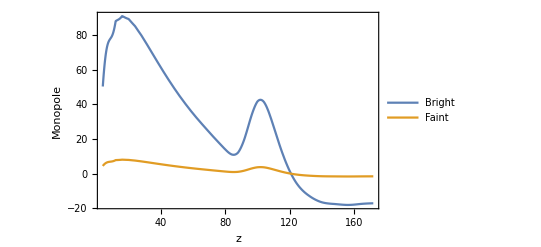

```mathematica
Plot[{d^2MonopoleBf[d],d^2MonopoleFf[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Monopole"},RotateLabel->True, ImageSize->{300},PlotLegends->{Bright, Faint}]
```

## Dipole

```mathematica
g1[z_]:=2/(r[z] HH[z])+1/2(-Omm(1+z)+2/(1+z)^2(1-Omm))/HH[z]^2
```

```mathematica
g1zSKA=Table[g1[i],{i,zSKA}]
```

{15.1422,9.64318,7.20087,5.78564,4.84435,4.16406,3.64492,3.23351,2.89842,2.61978,2.3843,2.18266,2.00812,1.85564,1.72137,1.60229,1.49603,1.40068,1.31468}

```mathematica
DipoleΛCDM=evolzSKA HzSKA(3(smodelBzSKA-smodelFzSKA)fzSKA^2 (1/(rH0zSKA HzSKA)-1)- 5(bBzSKA smodelFzSKA-bFzSKA smodelBzSKA)(1/(rH0zSKA HzSKA)-1) fzSKA+(bBzSKA-bFzSKA) g1zSKA fzSKA)
```

{18.7049,6.93007,4.49096,3.04636,1.98008,1.24304,0.785583,0.534071,0.40313,0.339628,0.312266,0.308562,0.323305,0.353265,0.393344,0.440838,0.494296,0.553599,0.617079}

```mathematica
Dipole=(HzSKA/Sigma8z0^2)(3 (βBzSKA-βFzSKA)GtildezSKA^2/5-(bBtildezSKA βFzSKA-bFtildezSKA βBzSKA)GtildezSKA -(bBtildezSKA-bFtildezSKA)(1-2 /(rH0zSKA  HzSKA))GtildezSKA+(3/2)(bBtildezSKA-bFtildezSKA)IhatzSKA-(bBtildezSKA-bFtildezSKA)dGtildezSKA /(H0 HzSKA))
```

{14.2169,4.25407,2.23329,1.17889,1.0152,1.16646,1.42713,1.62045,1.75625,1.86681,1.9782,2.11291,2.25613,2.39011,2.52396,2.66016,2.81017,2.98196,3.15526}

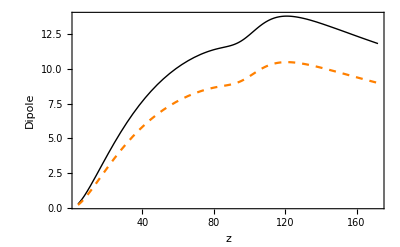

```mathematica
Plot[{d^2DipoleΛCDM[[1]] nu1z0[d],d^2Dipole[[1]] nu1z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},PlotStyle->{{Black,Thin},{Orange,Dashed}}, Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Dipole"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

```mathematica
Dipolez1[d_]:=Dipole[[1]] nu1z0[d]
```

```mathematica
WideAnglezSKA=-(2/5)(bBtildezSKA-bFtildezSKA)GtildezSKA/(rH0zSKA /H0)
```

{-0.000381671,-0.000228668,-0.000161107,-0.000122461,-0.0000972554,-0.0000794854,-0.0000663071,-0.0000561836,-0.0000482031,-0.0000417856,-0.0000365424,-0.000032202,-0.0000285691,-0.0000254989,-0.0000228825,-0.0000206358,-0.0000186936,-0.0000170042,-0.0000155265}

```mathematica
WideAnglez1[d_]:=WideAnglezSKA[[1]]d mu2z0[d]
```

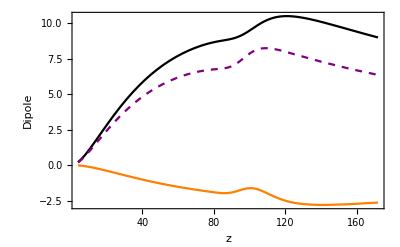

```mathematica
Plot[{d^2Dipole[[1]] nu1z0[d],  d^2(d WideAnglezSKA[[1]] mu2z0[d]),d^2Dipole[[1]] nu1z0[d]+  d^2 (d WideAnglezSKA[[1]] mu2z0[d])},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},PlotStyle->{{Black},{Orange},{Purple,Dashed}}, Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Dipole"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

```mathematica
Table[Dipolez1[d],{d,4,172,4}]
```

{0.0130118,0.0113305,0.0096173,0.00819064,0.00702957,0.00608181,0.00530126,0.00465213,0.0041072,0.00364569,0.00325172,0.00291302,0.00261994,0.00236485,0.00214157,0.00194507,0.0017713,0.00161667,0.00147832,0.00135398,0.00124204,0.0011431,0.00106044,0.00099645,0.000948131,0.000907583,0.000867216,0.000823656,0.00077724,0.000729598,0.000682333,0.000636752,0.00059366,0.000553323,0.000515784,0.000481087,0.000449171,0.000419797,0.000392711,0.000367767,0.000344852,0.000323771,0.000304302}

```mathematica
Table[WideAnglez1[d],{d,4,172,4}]
```

{-0.00113927,-0.00120546,-0.00115413,-0.00107296,-0.000986653,-0.000903478,-0.000826481,-0.000756277,-0.00069289,-0.000635808,-0.000584433,-0.000538151,-0.000496448,-0.000458769,-0.000424868,-0.000394124,-0.000366465,-0.000341751,-0.000319284,-0.000298887,-0.000278791,-0.000253937,-0.00022117,-0.000186658,-0.000162714,-0.000155679,-0.000160606,-0.000168204,-0.000172987,-0.000173891,-0.000171198,-0.000165648,-0.000158602,-0.000151102,-0.000143265,-0.000135142,-0.000127262,-0.000120019,-0.000113212,-0.000106557,-0.000100215,-0.0000944777,-0.0000892822}

```mathematica
Abs[(Table[Dipolez1[d],{d,4,172,4}]-(Table[Dipolez1[d],{d,4,172,4}]+Table[WideAnglez1[d],{d,4,172,4}]))/(Table[Dipolez1[d],{d,4,172,4}])]
```

{0.0875569,0.10639,0.120006,0.130999,0.140358,0.148554,0.155903,0.162566,0.168702,0.1744,0.179731,0.18474,0.189488,0.193995,0.198391,0.202627,0.20689,0.211392,0.215978,0.220747,0.224462,0.222147,0.208564,0.187323,0.171616,0.171532,0.185197,0.204216,0.222566,0.238339,0.250901,0.260145,0.26716,0.273082,0.277761,0.280909,0.283326,0.285897,0.288283,0.289741,0.290604,0.291804,0.293399}

```mathematica
rH0zSKA/H0
```

{433.566,704.263,960.18,1201.58,1428.95,1642.94,1844.3,2033.82,2212.29,2380.49,2539.19,2689.08,2830.84,2965.07,3092.35,3213.19,3328.07,3437.42,3541.64}

## Quadrupole

```mathematica
QuadrupoleBright=-(4 bBtildezSKA GtildezSKA/3 + 4 GtildezSKA^2/7)/Sigma8z0^2
```

{-1.19459,-1.21115,-1.21112,-1.19874,-1.17779,-1.15142,-1.12209,-1.09166,-1.06146,-1.03244,-1.00521,-0.98017,-0.957552,-0.937469,-0.919958,-0.905008,-0.892574,-0.882594,-0.875}

```mathematica
QuadrupoleFaint=-(4 bFtildezSKA GtildezSKA/3 + 4 GtildezSKA^2/7)/Sigma8z0^2
```

{-0.363068,-0.401924,-0.433806,-0.45934,-0.479464,-0.495215,-0.50759,-0.517471,-0.525605,-0.532604,-0.538955,-0.545042,-0.551163,-0.557553,-0.564391,-0.571821,-0.579954,-0.588883,-0.598682}

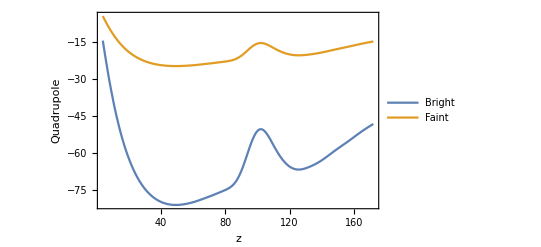

```mathematica
Plot[{d^2 QuadrupoleBright[[1]] mu2z0[d],d^2QuadrupoleFaint [[1]]mu2z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Quadrupole"},RotateLabel->True, ImageSize->{300},PlotLegends-> {Bright,Faint}]
```

```mathematica
QuadrupoleBz1[d_]:=QuadrupoleBright[[1]] mu2z0[d]
QuadrupoleFz1[d_]:=QuadrupoleFaint[[1]] mu2z0[d]
```

## Hexadecapole

```mathematica
Hexadecapole=(8 GtildezSKA^2/35)/Sigma8z0^2
```

{0.0723187,0.0761278,0.0779996,0.0782448,0.0772142,0.0752437,0.0726254,0.0695971,0.0663425,0.0629982,0.0596618,0.0564005,0.053258,0.0502613,0.0474248,0.0447544,0.0422501,0.0399079,0.0377213}

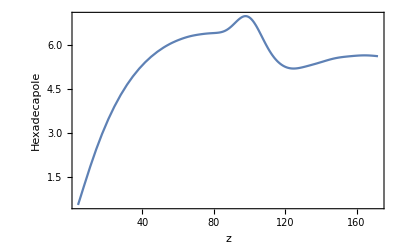

```mathematica
Plot[{d^2Hexadecapole[[1]] mu4z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Hexadecapole"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

```mathematica
Hexadecapolez1[d_]:=Hexadecapole[[1]] mu4z0[d];
```

## Octupole

```mathematica
Octupole=(HzSKA/Sigma8z0^2)2 (βBzSKA-βFzSKA)GtildezSKA^2/5
```

{2.11151,0.483304,0.253246,0.109003,0.104839,0.145488,0.196973,0.226399,0.239656,0.24456,0.248143,0.254043,0.259531,0.261676,0.262342,0.262151,0.262817,0.265374,0.26735}

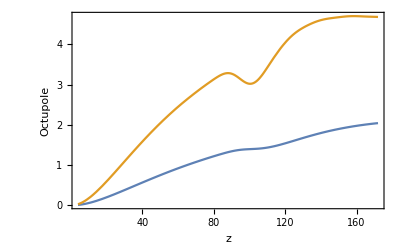

```mathematica
Plot[{d^2 Octupole[[1]] nu3z0[d], d^2 Octupole[[1]] nu3z0[d] - d^2 WideAnglezSKA[[1]]d mu2z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Octupole"},RotateLabel->True, ImageSize->{300}]
```

```mathematica
Octupolez1[d_]:=Octupole[[1]] nu3z0[d]
OctupoleWAz1[d_]:=Octupole[[1]] nu3z0[d] -WideAnglezSKA[[1]] d mu2z0[d]
```

## Joint plot

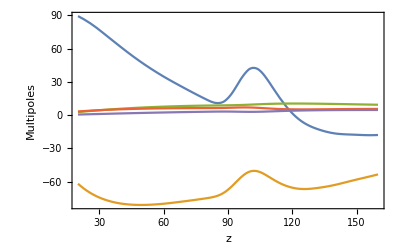

```mathematica
Plot[{d^2 MonopoleBf[d],d^2QuadrupoleBz1[d],d^2Dipolez1[d],d^2Hexadecapolez1[d], d^2 OctupoleWAz1[d]},{d,20,160},PlotRange->{All,All}, Axes->{True,True},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Multipoles"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

## Signal-to-noise Ratios

```mathematica
{dmin,dmax}
```

{20,160}

```mathematica
{maxsep,ktot,indist,ldist}
```

{40,19,5,36}

## Monopole

```mathematica
ξ0BSKAmatrix=Table[MonopoleBright[[k]]mu0z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ0BSKAmatrix]
```

{36,19}

```mathematica
Dimensions[varTOTMONOBrightLp4d4to172zSKA]
```

{19,43,43}

```mathematica
varξ0BTOT=Table[ varTOTMONOBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ0BTOT=Table[Inverse[varξ0BTOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ0BTOT]
```

{19,36,36}

```mathematica
SNrSKAMonopole=Table[Sqrt[Sum[ξ0BSKAmatrix[[m,k]] invcovξ0BTOT[[k,m,n]] ξ0BSKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{61.4598,95.6373,125.408,150.563,170.984,186.679,197.489,203.331,203.997,199.293,189.618,175.28,156.945,136.01,113.153,90.2549,68.7321,49.5585,33.8044}

```mathematica
SNSKAMonopoleTotal= Sqrt[Sum[ξ0BSKAmatrix[[m,k]] invcovξ0BTOT[[k,m,n]] ξ0BSKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

645.107

## Dipole

```mathematica
ξ1SKAmatrix=Table[Dipole[[k]]nu1z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ1SKAmatrix]
```

{36,19}

```mathematica
varξ1TOT=Table[varTOTDIP2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ1TOT=Table[Inverse[varξ1TOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ1TOT]
```

{19,36,36}

```mathematica
SNrSKADipole=Table[Sqrt[Sum[ξ1SKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] ξ1SKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{52.5456,28.5944,17.2002,8.87363,6.91335,7.00922,7.41391,7.16965,6.50956,5.69401,4.89986,4.18435,3.51133,2.87926,2.29706,1.78708,1.35521,0.993626,0.695826}

```mathematica
SNSKADipoleTotal= Sqrt[Sum[ξ1SKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] ξ1SKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

65.6146

```mathematica
1-54.6434/78.2865
```

0.302007

## Dipole + WA

```mathematica
ξ1SKAmatrix=Table[Dipole[[k]]nu1z0[d]+d WideAnglezSKA[[k]] mu2z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ1SKAmatrix]
```

{36,19}

```mathematica
varξ1TOT=Table[varTOTDIP2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ1TOT=Table[Inverse[varξ1TOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ1TOT]
```

{19,36,36}

```mathematica
SNrSKADipole=Table[Sqrt[Sum[ξ1SKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] ξ1SKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{45.0897,19.357,9.38934,3.21121,2.77108,3.92146,5.15423,5.52803,5.32432,4.84511,4.29451,3.75588,3.21099,2.67048,2.15447,1.69136,1.2924,0.95376,0.671504}

```mathematica
SNSKADipoleTotal= Sqrt[Sum[ξ1SKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] ξ1SKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

51.9498

## Quadrupole

```mathematica
ξ2BSKAmatrix=Table[QuadrupoleBright[[k]]mu2z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ2BSKAmatrix]
```

{36,19}

```mathematica
varξ2BTOT=Table[varTOTQUADBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ2BTOT=Table[Inverse[varξ2BTOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ2BTOT]
```

{19,36,36}

```mathematica
ldist
```

36

```mathematica
SNrSKAQuadrupole=Table[Sqrt[Sum[ξ2BSKAmatrix[[m,k]] invcovξ2BTOT[[k,m,n]] ξ2BSKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{35.6855,57.4196,76.9314,93.4471,106.473,115.781,121.179,122.643,120.173,113.888,104.395,92.3161,78.5253,64.2581,50.2066,37.488,26.6905,17.9953,11.4944}

```mathematica
SNSKAQuadrupoleTotal= Sqrt[Sum[ξ2BSKAmatrix[[m,k]] invcovξ2BTOT[[k,m,n]] ξ2BSKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

368.661

## Octupole

```mathematica
ξ3SKAmatrix=Table[Octupole[[k]]nu3z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ3SKAmatrix]
```

{36,19}

```mathematica
Octupole[[1;;ktot]]
```

{2.11151,0.483304,0.253246,0.109003,0.104839,0.145488,0.196973,0.226399,0.239656,0.24456,0.248143,0.254043,0.259531,0.261676,0.262342,0.262151,0.262817,0.265374,0.26735}

```mathematica
varξ3TOT=Table[varTOTOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ3TOT=Table[Inverse[varξ3TOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ3TOT]
```

{19,36,36}

```mathematica
SNrSKAOctupole=Table[Sqrt[Sum[ξ3SKAmatrix[[m,k]] invcovξ3TOT[[k,m,n]] ξ3SKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{6.56523,2.43129,1.36794,0.560293,0.485702,0.594134,0.694661,0.678704,0.600254,0.50232,0.412073,0.335376,0.267264,0.206617,0.154617,0.112375,0.0794709,0.054336,0.0354466}

```mathematica
SNSKAOctupoleTotal= Sqrt[Sum[ξ3SKAmatrix[[m,k]] invcovξ3TOT[[k,m,n]] ξ3SKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

7.33395

```mathematica
1-4.68151/8.50621
```

0.449636

## Octupole + WA

```mathematica
ξ3SKAmatrix=Table[Octupole[[k]]nu1z0[d] -d WideAnglezSKA[[k]] mu2z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ3SKAmatrix]
```

{36,19}

```mathematica
varξ3TOT=Table[varTOTOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ3TOT=Table[Inverse[varξ3TOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ3TOT]
```

{19,36,36}

```mathematica
SNrSKAOctupoleWA=Table[Sqrt[Sum[ξ3SKAmatrix[[m,k]] invcovξ3TOT[[k,m,n]] ξ3SKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{23.4132,14.6201,10.1867,6.73449,4.93622,3.89817,3.18207,2.54039,1.97732,1.50735,1.14057,0.858999,0.638077,0.464557,0.32913,0.227344,0.153037,0.0996788,0.0622469}

```mathematica
SNSKAOctupoleWATotal= Sqrt[Sum[ξ3SKAmatrix[[m,k]] invcovξ3TOT[[k,m,n]] ξ3SKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

31.2447

## Hexadecapole

```mathematica
ξ4TSKAmatrix=Table[Hexadecapole[[k]]mu4z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ4TSKAmatrix]
```

{36,19}

```mathematica
varξ4TTOT=Table[varTOTHEXAtotpopLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ4TTOT=Table[Inverse[varξ4TTOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ4TTOT]
```

{19,36,36}

```mathematica
SNrSKAHexadecapole=Table[Sqrt[Sum[ξ4TSKAmatrix[[m,k]] invcovξ4TTOT[[k,m,n]] ξ4TSKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{9.7378,15.1786,19.6006,22.8466,24.8844,25.783,25.6376,24.5914,22.7903,20.396,17.6385,14.7113,11.8091,9.1342,6.76497,4.8075,3.27383,2.12239,1.3088}

```mathematica
SNSKAQuadrupoleTotal= Sqrt[Sum[ξ4TSKAmatrix[[m,k]] invcovξ4TTOT[[k,m,n]] ξ4TSKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

74.4918

## Plot

```mathematica
SNSKAz015Dipole=Table[ξ1SKAmatrix[[m,2]]/Sqrt[varξ1TOT[[1,m,m]]],{m,1,ldist}];
SNSKAz015Monopole=Table[ξ0BSKAmatrix[[m,2]]/Sqrt[varξ0BTOT[[1,m,m]]],{m,1,ldist}];
SNSKAz015Quadrupole=Table[Abs[ξ2BSKAmatrix[[m,2]]]/Sqrt[varξ2BTOT[[1,m,m]]],{m,1,ldist}];
SNSKAz015Octupole=Table[Abs[ξ3SKAmatrix[[m,2]]]/Sqrt[varξ3TOT[[1,m,m]]],{m,1,ldist}];
SNSKAz015Hexadecapole=Table[Abs[ξ4TSKAmatrix[[m,2]]]/Sqrt[varξ4TTOT[[1,m,m]]],{m,1,ldist}];
```

```mathematica
ds=Table[d,{d,dmin,dmax,4}];
```

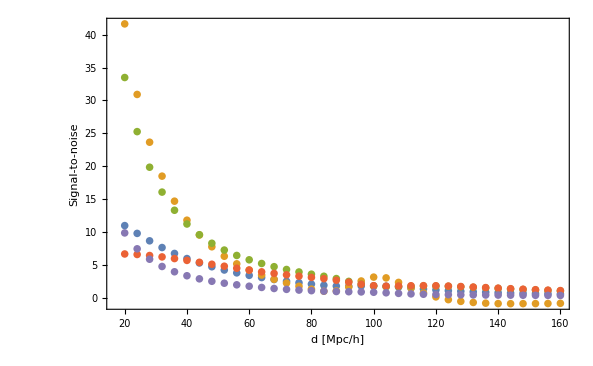

```mathematica
ListPlot[{Table[{ds[[i]], SNSKAz015Dipole[[i]]},{i,1,ldist}],Table[{ds[[i]], SNSKAz015Monopole[[i]]},{i,1,ldist}],Table[{ds[[i]], SNSKAz015Quadrupole[[i]]},{i,1,ldist}], Table[{ds[[i]], SNSKAz015Octupole[[i]]},{i,1,ldist}],
Table[{ds[[i]], SNSKAz015Hexadecapole[[i]]},{i,1,ldist}]},PlotRange->Full,PlotStyle->{•},Axes->{False,False},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"d [Mpc/h]","Signal-to-noise"},RotateLabel->True]
```

# Export

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["multi_split"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/multi_split

```mathematica
nBSKA
```

3/10

```mathematica
nFSKA
```

7/10

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrix_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>"_msplit-"<>StringReplace[ToString[Round[100 N[nBSKA]], InputForm],"/"->"-"]<>"B_"<>StringReplace[ToString[Round[100N[nFSKA]], InputForm],"/"->"-"]<>"F.txt",CovMatrixtabzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

EXPORT - WITH OCTUPOLE

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["octupole"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/octupole

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrixOCT_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>"_msplit-"<>StringReplace[ToString[Round[100 N[nBSKA]], InputForm],"/"->"-"]<>"B_"<>StringReplace[ToString[Round[100N[nFSKA]], InputForm],"/"->"-"]<>"F.txt",CovMatrixOCTtabzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

```mathematica
Exit[]
```